```mathematica
getSi[l_]:=Array[If[#1==#2,1,0]&,{2l+1,2l+1}]
```

```mathematica
getSz[l_]:=(Array[If[#1==#2,l+1-#1,0]&,{2l+1,2l+1}])
```

```mathematica
getSp[l_]:=(Array[If[#1==#2-1,Sqrt[(l+(l+1-#1))(l-(l+1-#1)+1)],0]&,{2l+1,2l+1}])
```

```mathematica
getSm[l_]:=(Array[If[#1==#2+1,Sqrt[(l+(l+1-#2))(l-(l+1-#2)+1)],0]&,{2l+1,2l+1}])
```

```mathematica
getSx[l_]:=(getSp[l]+getSm[l])/2
```

```mathematica
getSy[l_]:=(getSp[l]-getSm[l])/2/ⅈ
```

```mathematica
KP=KroneckerProduct;
```

```mathematica
scalar[si_,sxyz_,N_,{n1_,n2_}]:=Module[{i},Sum[KP@@Array[If[#==n1||#==n2,sxyz[[i]],si]&,{N}],{i,1,3}]]
```

```mathematica
scalar[i,{x,y,z},3,{1,3}]
```

KroneckerProduct[x,i,x]+KroneckerProduct[y,i,y]+KroneckerProduct[z,i,z]

```mathematica
mixed[si_,sxyz_,N_,{n1_,n2_,n3_}]:=Module[{i,j,k},Sum[Signature[{i,j,k}]KP@@Array[Switch[#,n1,sxyz[[i]],n2,sxyz[[j]],n3,sxyz[[k]],_,si]&,{N}],{i,1,3},{j,1,3},{k,1,3}]]
```

```mathematica
mixed[i,{x,y,z},4,{1,2,4}]
```

KroneckerProduct[x,y,i,z]-KroneckerProduct[x,z,i,y]-KroneckerProduct[y,x,i,z]+KroneckerProduct[y,z,i,x]+KroneckerProduct[z,x,i,y]-KroneckerProduct[z,y,i,x]

```mathematica
si=getSi[1]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
sx = getSx[1]
```

{{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}}

```mathematica
sy = getSy[1]
```

{{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}}

```mathematica
sz = getSz[1]
```

{{1,0,0},{0,0,0},{0,0,-1}}

```mathematica
s12=scalar[si,{sx,sy,sz},2,{1,2}];
```

```mathematica
Tr[s12]
```

0

```mathematica
i2=KP[si,si];
```

```mathematica
τ=i2+bs s12+bt(s12.s12-4/3 i2);
```

```mathematica
ρ=1/9(i2+as s12+at(s12.s12-4/3 i2));
```

```mathematica
Clear[as]
```

```mathematica
Clear[at]
```

```mathematica
{As,At}=Solve[ρ==τ.τ/Tr[τ.τ],{as,at}][[1]]//Simplify
```

{as→-(6 bs (-3+bt))/(9+12 bs^2-12 bs bt+8 bt^2),at→(3 (3 bs^2-12 bs bt+bt (6+7 bt)))/(9+12 bs^2-12 bs bt+8 bt^2)}

```mathematica
As=As/.(as->x_):>x
```

-(6 bs (-3+bt))/(9+12 bs^2-12 bs bt+8 bt^2)

```mathematica
At=At/.(at->x_):>x
```

(3 (3 bs^2-12 bs bt+bt (6+7 bt)))/(9+12 bs^2-12 bs bt+8 bt^2)

```mathematica
dss=D[As,bs]//Simplify
```

-(6 (-3+bt) (9-12 bs^2+8 bt^2))/((9+12 bs^2-12 bs bt+8 bt^2)^2)

```mathematica
dst=D[As,bt]//Simplify
```

-(6 bs (9-36 bs+12 bs^2+48 bt-8 bt^2))/((9+12 bs^2-12 bs bt+8 bt^2)^2)

```mathematica
dts=D[At,bs]//Simplify
```

```mathematica
(18 (18 bs^2 bt-2 (-3+bt)^2 bt+bs (9-24 bt-20 bt^2)))/((9+12 bs^2-12 bs bt+8 bt^2)^2)
```

```mathematica
dtt=D[At,bt]//Simplify
```

-(18 (-9+18 bs^3-21 bt+8 bt^2-4 bs^2 (3+5 bt)-2 bs (-9+bt^2)))/((9+12 bs^2-12 bs bt+8 bt^2)^2)

```mathematica
Det[{{dss, dst}, {dts, dtt}}]//Simplify
```

(108 (54 bs^3-6 bs (-3+bt)^2-9 bs^2 (3+8 bt)+(-3+bt)^2 (3+8 bt)))/((9+12 bs^2-12 bs bt+8 bt^2)^3)

```mathematica
(6bs-3-8bt)(3bs+3-bt)(3bs-3+bt)//Expand//Simplify
```

54 bs^3-6 bs (-3+bt)^2-9 bs^2 (3+8 bt)+(-3+bt)^2 (3+8 bt)

```mathematica
P0=i2;
```

```mathematica
Tr[P0]
```

9

```mathematica
PositiveSemidefiniteMatrixQ[P0]
```

True

```mathematica
s1212=s12.s12-4/3 i2;
```

```mathematica
P1=2/3(i2+3/4 s12+3/4 s1212);
```

```mathematica
P1.P1==P1
```

True

```mathematica
Tr[P1]
```

6

```mathematica
PositiveSemidefiniteMatrixQ[P6]
```

True

```mathematica
P2=8/9(i2-3/8 s1212);
```

```mathematica
P2.P2==P2
```

True

```mathematica
Tr[P2]
```

8

```mathematica
P3=4/9(i2-9/8 s12 - 3/8 s1212);
```

```mathematica
P3.P3==P3
```

True

```mathematica
Tr[P3]
```

4

```mathematica
P4=5/9(i2+9/10 s12+3/10 s1212);
```

```mathematica
P4.P4==P4
```

True

```mathematica
Tr[P4]
```

5

```mathematica
P5 = 1/3(i2-3/2 s12-3/2 s1212);
```

```mathematica
P5.P5==P5
```

True

```mathematica
Tr[P5]
```

3

```mathematica
P6=1/9(i2+3 s1212);
```

```mathematica
P6.P6==P6
```

True

```mathematica
Tr[P6]
```

1

```mathematica
{p0,p1,p2,p3,p4,p5,p6}={{8/3,0},{3/4,3/4},{0,-3/8},{-9/8,-3/8},{9/10,3/10},{-3/2,-3/2},{0,3}}
```

{{8/3,0},{3/4,3/4},{0,-3/8},{-9/8,-3/8},{9/10,3/10},{-3/2,-3/2},{0,3}}

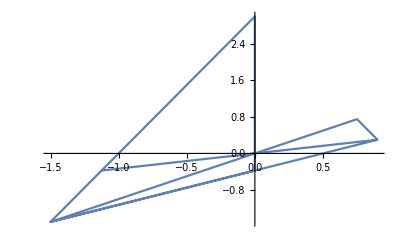

```mathematica
ListLinePlot[{p4,p5,p6,p2,p5,p1,p4,p3}]
```

```mathematica
ci=getSi[1/2]
```

{{1,0},{0,1}}

```mathematica
cx=getSx[1/2]
```

{{0,1/2},{1/2,0}}

```mathematica
cy=getSy[1/2]
```

{{0,-ⅈ/2},{ⅈ/2,0}}

```mathematica
cz=getSz[1/2]
```

{{1/2,0},{0,-1/2}}

```mathematica
c12=scalar[ci,{cx,cy,cz},5,{1,2}];
```

```mathematica
c13=scalar[ci,{cx,cy,cz},5,{1,3}];
```

```mathematica
c14=scalar[ci,{cx,cy,cz},5,{1,4}];
```

```mathematica
c15=scalar[ci,{cx,cy,cz},5,{1,5}];
```

```mathematica
c23=scalar[ci,{cx,cy,cz},5,{2,3}];
```

```mathematica
c24=scalar[ci,{cx,cy,cz},5,{2,4}];
```

```mathematica
c25=scalar[ci,{cx,cy,cz},5,{2,5}];
```

```mathematica
c34=scalar[ci,{cx,cy,cz},5,{3,4}];
```

```mathematica
c35=scalar[ci,{cx,cy,cz},5,{3,5}];
```

```mathematica
c45=scalar[ci,{cx,cy,cz},5,{4,5}];
```

```mathematica
c123=mixed[ci,{cx,cy,cz},5,{1,2,3}];
```

```mathematica
c124=mixed[ci,{cx,cy,cz},5,{1,2,4}];
```

```mathematica
c125=mixed[ci,{cx,cy,cz},5,{1,2,5}];
```

```mathematica
c134=mixed[ci,{cx,cy,cz},5,{1,3,4}];
```

```mathematica
c135=mixed[ci,{cx,cy,cz},5,{1,3,5}];
```

```mathematica
c145=mixed[ci,{cx,cy,cz},5,{1,4,5}];
```

```mathematica
c234=mixed[ci,{cx,cy,cz},5,{2,3,4}];
```

```mathematica
c235=mixed[ci,{cx,cy,cz},5,{2,3,5}];
```

```mathematica
c245=mixed[ci,{cx,cy,cz},5,{2,4,5}];
```

```mathematica
c345=mixed[ci,{cx,cy,cz},5,{3,4,5}];
```

```mathematica
MatrixRank[Flatten/@{c12.c345}]
```

1

```mathematica
MatrixRank[Flatten/@{c12.c345,c13.c245}]
```

2

```mathematica
MatrixRank[Flatten/@{c12.c345,c13.c245,c14.c235}]
```

3

```mathematica
MatrixRank[Flatten/@{c12.c345,c13.c245,c14.c235,c15.c234}]
```

3

```mathematica
MatrixRank[Flatten/@{c12.c345,c13.c245,c14.c235,c23.c145}]
```

4

```mathematica
MatrixRank[Flatten/@{c12.c345,c13.c245,c14.c235,c23.c145,c24.c135}]
```

5

```mathematica
MatrixRank[Flatten/@{c12.c345,c13.c245,c14.c235,c23.c145,c24.c135,c34.c125}]
```

6

```mathematica
MatrixRank[Flatten/@{c12.c345,c13.c245,c14.c235,c23.c145,c24.c135,c34.c125,c35.c124}]
```

6

```mathematica
MatrixRank[Flatten/@{c12.c345,c13.c245,c14.c235,c23.c145,c24.c135,c34.c125,c45.c123}]
```

6

```mathematica
Solve[c15.c234==a c12.c345 +b c13.c245+c c14.c235,{a,b,c}]
```

{{a→1,b→-1,c→1}}

```mathematica
Solve[c25.c134==a c12.c345 +b c13.c245+c c14.c235+d c23.c145+e c24.c135,{a,b,c,d,e}]
```

{{a→1,b→0,c→0,d→-1,e→1}}

```mathematica
Solve[c35.c124==a c12.c345 +b c13.c245+c c14.c235+d c23.c145+e c24.c135+f c34.c125,{a,b,c,d,e,f}]
```

{{a→0,b→1,c→0,d→-1,e→0,f→1}}

```mathematica
Solve[c45.c123==a c12.c345 +b c13.c245+c c14.c235+d c23.c145+e c24.c135+f c34.c125,{a,b,c,d,e,f}]
```

{{a→0,b→0,c→1,d→0,e→-1,f→1}}

```mathematica
(*myBinarySearch[list_,ll_,hh_,val_]:=Module[]*)
```

```mathematica
getBasisBasis=Function[{L,N},Module[{
sxyz=SparseArray/@{getSx[L],getSy[L],getSz[L]},
si=getSi[L]//SparseArray,
basis,
names
},
tmp=KP@@Array[si&,{N}];
basis={tmp};
names={Symbol["id"]};
flattened={tmp//Flatten};
If[N≥2,
For[i=1,i≤N-1,i++,
For[j=i+1,j≤N,j++,
tmp=SparseArray[scalar[si,sxyz,N,{i,j}]];
AppendTo[basis,tmp];
AppendTo[flattened,tmp//Flatten];
AppendTo[names,Symbol["s"<>ToString[i]<>ToString[j]]];
]
]
];
If[N≥3,
For[i=1,i≤N-2,i++,
For[j=i+1,j≤N-1,j++,
For[k=j+1,k≤N,k++,
tmp=SparseArray[mixed[si,sxyz,N,{i,j,k}]];
AppendTo[basis,tmp];
AppendTo[flattened,tmp//Flatten];
AppendTo[names,Symbol["s"<>ToString[i]<>ToString[j]<>ToString[k]]];
]
]
]
];
If[MatrixRank[flattened]≠Length[flattened],Print["затравочные - Линейно-зависимы ",MatrixRank[flattened],"   ",Length[flattened]];Return[]];
{basis,names}
]];
```

```mathematica
basisBasis1d2n3=getBasisBasis[1/2,3]
```

{{SparseArray[<8>, {8, 8}],SparseArray[<12>, {8, 8}],SparseArray[<12>, {8, 8}],SparseArray[<12>, {8, 8}],SparseArray[<12>, {8, 8}]},{id,s12,s13,s23,s123}}

```mathematica
Print[#//Normal//Flatten]&/@basisBasis1d2n3[[1]];
```

{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1}

{1/4,0,0,0,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,-1/4,0,1/2,0,0,0,0,0,0,-1/4,0,1/2,0,0,0,0,1/2,0,-1/4,0,0,0,0,0,0,1/2,0,-1/4,0,0,0,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,1/4}

{1/4,0,0,0,0,0,0,0,0,-1/4,0,0,1/2,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,-1/4,0,0,1/2,0,0,1/2,0,0,-1/4,0,0,0,0,0,0,0,0,1/4,0,0,0,0,0,1/2,0,0,-1/4,0,0,0,0,0,0,0,0,1/4}

{1/4,0,0,0,0,0,0,0,0,-1/4,1/2,0,0,0,0,0,0,1/2,-1/4,0,0,0,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,-1/4,1/2,0,0,0,0,0,0,1/2,-1/4,0,0,0,0,0,0,0,0,1/4}

{0,0,0,0,0,0,0,0,0,0,ⅈ/4,0,-ⅈ/4,0,0,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,0,0,0,0,0,0,-ⅈ/4,ⅈ/4,0,0,ⅈ/4,-ⅈ/4,0,0,0,0,0,0,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,0,0,-ⅈ/4,0,ⅈ/4,0,0,0,0,0,0,0,0,0,0}

```mathematica
firstNotNull[splist_]:=splist["NonzeroPositions"][[1,1]]
```

```mathematica
triangularizeFlattened=Function[{argflattened,argformulas},Module[{
flattened=argflattened,
formulas=argformulas,
firstPosition,
list,
i,j,
tmp,tmp2
},
(*приводим flattened к треугольному виду*)
swap[i_,j_]:=Module[
{tmpfl=flattened[[i]],tmpn=formulas[[i]]},
flattened[[i]]=flattened[[j]];formulas[[i]]=formulas[[j]];
flattened[[j]]=tmpfl;formulas[[j]]=tmpn;
];
(*For[i=1,i≤Length[flattened],i++,
Print[flattened[[i]]//Normal,formulas[[i]]];
];*)
For[i=1,i≤Length[flattened]-1,i++,
firstPosition=firstNotNull[flattened[[i]]];
list={i};
Print[i," --------- ",firstPosition," ",list,flattened[[i]]["NonzeroPositions"]];
(*Ищу строки с наиболее первыми ненулевыми элементами (начиная с i+1) *)
For[j=i+1,j≤Length[flattened],j++,
tmp=firstNotNull[flattened[[j]]];
If[tmp<firstPosition,
firstPosition=tmp;
list={j}
,
If[tmp==firstPosition,
AppendTo[list,j]
]
]
];(*нашли первую позицию и список, который надо нормализовать*)
Print[i," found ",firstPosition," ",list];
swap[i,list[[1]]];(*перемещаю первую найденную строку на нужное место*)
tmp=flattened[[i,firstPosition]];
For[j=2,j≤Length[list],j++,(*нормализую оставшиеся найденные строки*)
tmp2=flattened[[list[[j]],firstPosition]];
flattened[[list[[j]]]]=SparseArray[flattened[[list[[j]]]]-flattened[[i]]/tmp*tmp2];
formulas[[list[[j]]]]-=(formulas[[i]]/tmp*tmp2//Expand);
]
;Module[{i},
For[i=1,i≤Length[flattened],i++,
Print[formulas[[i]]," ",flattened[[i]]//Normal];
];
];
];(*For i*)
{flattened,formulas}
]];
```

```mathematica
triangularizeFlattened[SparseArray[{{1, 0, 0}, {1, 0, 0}, {1, 0, 0}}],{x1,x2,x3}]
```

1 --------- 1 {1}{{1}}

1 found 1 {1,2,3}

x1 {1,0,0}

-x1+x2 {0,0,0}

-x1+x3 {0,0,0}

Part::partw: Part 1 of {} does not exist.

2 --------- {}⟦1,1⟧ {2}{}

Part::partw: Part 1 of {} does not exist.

2 found {}⟦1,1⟧ {2}

Part::pkspec1: The expression {} ⟦ 1, 1 ⟧ cannot be used as a part specification.

x1 {1,0,0}

-x1+x2 {0,0,0}

-x1+x3 {0,0,0}

{SparseArray[<1>, {3, 3}],{x1,-x1+x2,-x1+x3}}

```mathematica
getBasis=Function[{argbasis,argnames},Module[{
basis=argbasis,
names=argnames,
flattened,
flfls,(*flatten formulas*)
firstPoses={},
i,j,k,n=2,
tmp,tmp2
},
(*инициализация базиса*)
fls=names;


];
firstPoses=firstNotNull/@flattened;
For[i=1,i≤Length[flattened],i++,
Print[fls[[i]]," ",firstPoses[[i]],flattened[[i]]//Normal];
];
Return[];
(*поиск новых элементов*)
For[n=2,n≤Length[basis],n++,(*While*)
Print["=== ",n," ",Length[basis]," ==="];
For[i=2,i≤n,i++,
Print[i," ",n+2-i];
tmp=SparseArray[basis[[i]].basis[[n+2-i]]];
(*tmp2=tmp["NonzeroPositions"]//Length;
tmp=SparseArray[tmp];
If[(tmp["NonzeroPositions"]//Length)≠tmp2,Print[tmp2," to ",tmp["NonzeroPositions"]//Length]];*)

Module[{
formula=Symbol[SymbolName[names[[i]]]<>SymbolName[names[[n+2-i]]]],
name,
i,j,k,
curstr=1,
tmpfl=Flatten[tmp],
tmppos
},
name=formula;
Print[tmpfl//Normal];
While[Length[tmpfl["NonzeroPositions"]]≠0,
tmppos=firstNotNull[tmpfl];
While[curstr≤Length[firstPoses]&&firstPoses[[curstr]]<tmppos,curstr++];
Print["tmppos,curstr= ",tmppos," ",curstr(*, "  ",tmpfl//Normal*)];
If[curstr≤Length[firstPoses]&&firstPoses[[curstr]]==tmppos,
j=flattened[[curstr,tmppos]];
k=tmpfl[[tmppos]];
tmpfl=SparseArray[tmpfl-flattened[[curstr]]/j*k];
formula-=(fls[[curstr]]/j*k//Expand);
Print[k/j];
Print[formula,tmpfl//Normal];
,
AppendTo[basis,tmp];
AppendTo[names,name];
flattened=Insert[flattened,tmpfl,curstr];
fls=Insert[fls,formula,curstr];
firstPoses = Insert[firstPoses,tmppos,curstr];

Break[]
]
];
If[Length[tmpfl["NonzeroPositions"]]==0,
Print[name," - LZ"];
]
];
]
];
(*return*){basis,names}
]];
```

```mathematica
getBasis[1/2,3]
```

id 1{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1}

-id/4+s13 10{0,0,0,0,0,0,0,0,0,-1/2,0,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,1/2,0,0,1/2,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,0,-1/2,0,0,0,0,0,0,0,0,0}

s123 11{0,0,0,0,0,0,0,0,0,0,ⅈ/4,0,-ⅈ/4,0,0,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,0,0,0,0,0,0,-ⅈ/4,ⅈ/4,0,0,ⅈ/4,-ⅈ/4,0,0,0,0,0,0,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,0,0,-ⅈ/4,0,ⅈ/4,0,0,0,0,0,0,0,0,0,0}

-s13+s23 19{0,0,0,0,0,0,0,0,0,0,1/2,0,-1/2,0,0,0,0,1/2,-1/2,0,0,0,0,0,0,0,0,1/2,0,0,-1/2,0,0,-1/2,0,0,1/2,0,0,0,0,0,0,0,0,-1/2,1/2,0,0,0,0,-1/2,0,1/2,0,0,0,0,0,0,0,0,0,0}

-id/4+s12+s13-s23 28{0,0,0,0,0,0,0,0,0,0,-1/2,0,1/2,0,0,0,0,-1/2,0,0,1/2,0,0,0,0,0,0,-1,0,1/2,1/2,0,0,1/2,1/2,0,-1,0,0,0,0,0,0,1/2,0,0,-1/2,0,0,0,0,1/2,0,-1/2,0,0,0,0,0,0,0,0,0,0}

=== 2 5 ===

2 2

{1/16,0,0,0,0,0,0,0,0,1/16,0,0,0,0,0,0,0,0,5/16,0,-1/4,0,0,0,0,0,0,5/16,0,-1/4,0,0,0,0,-1/4,0,5/16,0,0,0,0,0,0,-1/4,0,5/16,0,0,0,0,0,0,0,0,1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s12s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 4

-1/2

-id/16+s12s12-s13/2+s23/2{0,0,0,0,0,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,1/4,0,0,-1/4,0,0,0,0,0,0,1/2,0,-1/4,-1/4,0,0,-1/4,-1/4,0,1/2,0,0,0,0,0,0,-1/4,0,0,1/4,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 28 5

-1/2

-(3 id)/16+s12/2+s12s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s12 - LZ

=== 3 5 ===

2 3

{1/16,0,0,0,0,0,0,0,0,-1/16,0,0,1/8,0,0,0,0,1/4,-1/16,0,-1/8,0,0,0,0,0,0,1/16,0,1/8,-1/8,0,0,-1/8,1/8,0,1/16,0,0,0,0,0,0,-1/8,0,-1/16,1/4,0,0,0,0,1/8,0,0,-1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s12s13{0,0,0,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,1/4,-1/8,0,-1/8,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,-1/8,0,-1/8,1/4,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/4

s12s13-s13/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,-1/8,0,-1/8,0,0,0,0,0,0,1/8,0,1/8,-1/4,0,0,-1/4,1/8,0,1/8,0,0,0,0,0,0,-1/8,0,-1/8,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 28 5

-1/8

-id/32+s12/8+s12s13-s13/8-s23/8{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,3/16,-1/8,0,-1/16,0,0,0,0,0,0,0,0,3/16,-3/16,0,0,-3/16,3/16,0,0,0,0,0,0,0,0,-1/16,0,-1/8,3/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 31 6

3 2

{1/16,0,0,0,0,0,0,0,0,-1/16,1/4,0,-1/8,0,0,0,0,0,-1/16,0,1/8,0,0,0,0,0,0,1/16,0,-1/8,1/8,0,0,1/8,-1/8,0,1/16,0,0,0,0,0,0,1/8,0,-1/16,0,0,0,0,0,-1/8,0,1/4,-1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s13s12{0,0,0,0,0,0,0,0,0,-1/8,1/4,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/4,-1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/4

-s13/4+s13s12{0,0,0,0,0,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ

ⅈ s123-s13/4+s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,-1/8,0,-1/8,0,0,0,0,0,0,1/8,0,1/8,-1/4,0,0,-1/4,1/8,0,1/8,0,0,0,0,0,0,-1/8,0,-1/8,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

=== 4 7 ===

2 4

{1/16,0,0,0,0,0,0,0,0,-1/16,1/8,0,0,0,0,0,0,-1/8,1/16,0,1/8,0,0,0,0,0,0,-1/16,0,-1/8,1/4,0,0,1/4,-1/8,0,-1/16,0,0,0,0,0,0,1/8,0,1/16,-1/8,0,0,0,0,0,0,1/8,-1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s12s23{0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,-1/8,1/4,0,0,1/4,-1/8,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/4

s12s23-s13/4{0,0,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/2

(ⅈ s123)/2+s12s23-s13/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s23 - LZ

3 3

{1/16,0,0,0,0,0,0,0,0,5/16,0,0,-1/4,0,0,0,0,0,1/16,0,0,0,0,0,0,0,0,5/16,0,0,-1/4,0,0,-1/4,0,0,5/16,0,0,0,0,0,0,0,0,1/16,0,0,0,0,0,-1/4,0,0,5/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s13s13{0,0,0,0,0,0,0,0,0,1/4,0,0,-1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,0,-1/4,0,0,-1/4,0,0,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/4,0,0,1/4,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/2

-(3 id)/16+s13/2+s13s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s13 - LZ

4 2

{1/16,0,0,0,0,0,0,0,0,-1/16,-1/8,0,1/4,0,0,0,0,1/8,1/16,0,-1/8,0,0,0,0,0,0,-1/16,0,1/8,0,0,0,0,1/8,0,-1/16,0,0,0,0,0,0,-1/8,0,1/16,1/8,0,0,0,0,1/4,0,-1/8,-1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s23s12{0,0,0,0,0,0,0,0,0,-1/8,-1/8,0,1/4,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,1/4,0,-1/8,-1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/4

-s13/4+s23s12{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/2

-(ⅈ s123)/2-s13/4+s23s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s23s12 - LZ

=== 5 7 ===

2 5

{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,(3 ⅈ)/16,-ⅈ/8,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,ⅈ/16,-(3 ⅈ)/16,0,0,-(3 ⅈ)/16,ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,-ⅈ/8,(3 ⅈ)/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

1/4

-s123/4+s12s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/4,-ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,ⅈ/8,-ⅈ/4,0,0,-ⅈ/4,ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,-ⅈ/8,ⅈ/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ

(3 s123)/4+s12s123+(ⅈ s13)/4-ⅈ s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s123 - LZ

3 4

{1/16,0,0,0,0,0,0,0,0,1/16,-1/8,0,1/8,0,0,0,0,1/8,-1/16,0,0,0,0,0,0,0,0,-1/16,0,1/4,-1/8,0,0,-1/8,1/4,0,-1/16,0,0,0,0,0,0,0,0,-1/16,1/8,0,0,0,0,1/8,0,-1/8,1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s13s23{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,-1/8,0,1/4,-1/8,0,0,-1/8,1/4,0,-1/8,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/2

-id/16-(ⅈ s123)/2+s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 5

1/4

-id/16-(ⅈ s123)/2+s13/4+s13s23-s23/4{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/4,0,1/8,1/8,0,0,1/8,1/8,0,-1/4,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 5

4 3

{1/16,0,0,0,0,0,0,0,0,1/16,1/8,0,-1/8,0,0,0,0,-1/8,-1/16,0,1/4,0,0,0,0,0,0,-1/16,0,0,1/8,0,0,1/8,0,0,-1/16,0,0,0,0,0,0,1/4,0,-1/16,-1/8,0,0,0,0,-1/8,0,1/8,1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s23s13{0,0,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,-1/8,-1/8,0,1/4,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/4,0,-1/8,-1/8,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/2

-id/16+(ⅈ s123)/2+s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 6

1/4

-id/16+(ⅈ s123)/2+s13/4-s23/4+s23s13{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/4,0,1/8,1/8,0,0,1/8,1/8,0,-1/4,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 6

5 2

{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/16,0,(3 ⅈ)/16,0,0,0,0,-ⅈ/16,ⅈ/8,0,-ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/8,-ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,-(3 ⅈ)/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/4

(3 s123)/4+s123s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/4,ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,-ⅈ/8,ⅈ/4,0,0,ⅈ/4,-ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,ⅈ/8,-ⅈ/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ

-s123/4+s123s12-(ⅈ s13)/4+ⅈ s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s123s12 - LZ

=== 6 9 ===

2 6

{1/64,0,0,0,0,0,0,0,0,-1/64,0,0,1/32,0,0,0,0,-1/8,5/64,0,1/16,0,0,0,0,0,0,-5/64,0,-1/16,5/32,0,0,5/32,-1/16,0,-5/64,0,0,0,0,0,0,1/16,0,5/64,-1/8,0,0,0,0,1/32,0,0,-1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s12s12s13{0,0,0,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-3/32,0,-1/16,5/32,0,0,5/32,-1/16,0,-3/32,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/16

s12s12s13-s13/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-1/16,0,-1/16,1/8,0,0,1/8,-1/16,0,-1/16,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

(ⅈ s123)/2+s12s12s13-(3 s13)/16+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s12s13 - LZ

3 5

{0,0,0,0,0,0,0,0,0,ⅈ/8,-(3 ⅈ)/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,(3 ⅈ)/16,-ⅈ/16,0,0,-ⅈ/16,(3 ⅈ)/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-(3 ⅈ)/16,ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/4

-(ⅈ id)/16+(ⅈ s13)/4+s13s123{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/16,0,(3 ⅈ)/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/4,0,(3 ⅈ)/16,ⅈ/16,0,0,ⅈ/16,(3 ⅈ)/16,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,-(3 ⅈ)/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/4

-(ⅈ id)/16+(3 s123)/4+(ⅈ s13)/4+s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,0,0,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ

-(ⅈ id)/16-s123/4+ⅈ s13s12+s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 7

ⅈ/4

-(ⅈ id)/16-s123/4+(ⅈ s13)/4+ⅈ s13s12+s13s123-(ⅈ s23)/4{0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/4,0,ⅈ/8,ⅈ/8,0,0,ⅈ/8,ⅈ/8,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 7

4 4

{1/16,0,0,0,0,0,0,0,0,5/16,-1/4,0,0,0,0,0,0,-1/4,5/16,0,0,0,0,0,0,0,0,1/16,0,0,0,0,0,0,0,0,1/16,0,0,0,0,0,0,0,0,5/16,-1/4,0,0,0,0,0,0,-1/4,5/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

1/16

-id/16+s23s23{0,0,0,0,0,0,0,0,0,1/4,-1/4,0,0,0,0,0,0,-1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,-1/4,0,0,0,0,0,0,-1/4,1/4,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/2

-(3 id)/16+s13/2+s23s23{0,0,0,0,0,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,-1/4,1/4,0,0,0,0,0,0,0,0,-1/4,0,0,1/4,0,0,1/4,0,0,-1/4,0,0,0,0,0,0,0,0,1/4,-1/4,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ

-(3 id)/16-ⅈ s123+s13/2+s23s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,1/4,0,1/4,0,0,0,0,0,0,-1/4,0,-1/4,1/2,0,0,1/2,-1/4,0,-1/4,0,0,0,0,0,0,1/4,0,1/4,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-2

-(3 id)/16+ⅈ s123+2 s13s12+s23s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s23s23 - LZ

5 3

{0,0,0,0,0,0,0,0,0,-ⅈ/8,ⅈ/16,0,ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,0,-(3 ⅈ)/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-(3 ⅈ)/16,0,0,(3 ⅈ)/16,0,0,0,0,ⅈ/16,0,ⅈ/16,-ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/4

(ⅈ id)/16+s123s13-(ⅈ s13)/4{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,0,-(3 ⅈ)/16,0,0,0,0,0,0,ⅈ/4,0,-ⅈ/16,-(3 ⅈ)/16,0,0,-(3 ⅈ)/16,-ⅈ/16,0,ⅈ/4,0,0,0,0,0,0,-(3 ⅈ)/16,0,0,(3 ⅈ)/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

1/4

(ⅈ id)/16-s123/4+s123s13-(ⅈ s13)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,0,0,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ

(ⅈ id)/16+(3 s123)/4+s123s13-ⅈ s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 8

-ⅈ/4

(ⅈ id)/16+(3 s123)/4+s123s13-(ⅈ s13)/4-ⅈ s13s12+(ⅈ s23)/4{0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/4,0,-ⅈ/8,-ⅈ/8,0,0,-ⅈ/8,-ⅈ/8,0,ⅈ/4,0,0,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 8

6 2

{1/64,0,0,0,0,0,0,0,0,-1/64,1/16,0,-1/32,0,0,0,0,1/16,-3/64,0,0,0,0,0,0,0,0,3/64,0,0,-1/32,0,0,-1/32,0,0,3/64,0,0,0,0,0,0,0,0,-3/64,1/16,0,0,0,0,-1/32,0,1/16,-1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s12s13s12{0,0,0,0,0,0,0,0,0,-1/32,1/16,0,-1/32,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,-1/32,0,1/16,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/16

s12s13s12-s13/16{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/4

(ⅈ s123)/4+s12s13s12-s13/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/16,0,-1/16,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-1/16,0,-1/16,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/2

-(ⅈ s123)/4+s12s13s12+s13/16-s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s13s12 - LZ

=== 7 11 ===

2 7

{1/64,0,0,0,0,0,0,0,0,-1/64,1/16,0,-1/32,0,0,0,0,1/16,-3/64,0,0,0,0,0,0,0,0,3/64,0,0,-1/32,0,0,-1/32,0,0,3/64,0,0,0,0,0,0,0,0,-3/64,1/16,0,0,0,0,-1/32,0,1/16,-1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s12s13s12{0,0,0,0,0,0,0,0,0,-1/32,1/16,0,-1/32,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,-1/32,0,1/16,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/16

s12s13s12-s13/16{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/4

(ⅈ s123)/4+s12s13s12-s13/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/16,0,-1/16,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-1/16,0,-1/16,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/2

-(ⅈ s123)/4+s12s13s12+s13/16-s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s13s12 - LZ

3 6

{1/64,0,0,0,0,0,0,0,0,-3/64,1/16,0,0,0,0,0,0,1/16,-1/64,0,-1/32,0,0,0,0,0,0,3/64,0,-1/32,0,0,0,0,-1/32,0,3/64,0,0,0,0,0,0,-1/32,0,-1/64,1/16,0,0,0,0,0,0,1/16,-3/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s12s13{0,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/8

id/64-s13/8+s13s12s13{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,3/32,0,-1/32,-1/16,0,0,-1/16,-1/32,0,3/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/4

id/64+(ⅈ s123)/4-s13/8+s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/32,0,-3/32,0,0,0,0,0,0,3/32,0,1/32,-1/8,0,0,-1/8,1/32,0,3/32,0,0,0,0,0,0,-3/32,0,-1/32,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/2

id/64-(ⅈ s123)/4-s13s12/2+s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 9

-1/16

id/64-(ⅈ s123)/4-s13/16-s13s12/2+s13s12s13+s23/16{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 9

4 5

{0,0,0,0,0,0,0,0,0,-ⅈ/8,-ⅈ/16,0,(3 ⅈ)/16,0,0,0,0,ⅈ/16,ⅈ/8,0,-(3 ⅈ)/16,0,0,0,0,0,0,0,0,-ⅈ/16,ⅈ/16,0,0,ⅈ/16,-ⅈ/16,0,0,0,0,0,0,0,0,-(3 ⅈ)/16,0,ⅈ/8,ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,-ⅈ/16,-ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/4

(ⅈ id)/16-(ⅈ s13)/4+s23s123{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,ⅈ/8,0,-(3 ⅈ)/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-(3 ⅈ)/16,0,ⅈ/8,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/4

(ⅈ id)/16+s123/4-(ⅈ s13)/4+s23s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 10

-ⅈ/4

(ⅈ id)/16+s123/4-(ⅈ s13)/2+(ⅈ s23)/4+s23s123{0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/4,0,-ⅈ/8,-ⅈ/8,0,0,-ⅈ/8,-ⅈ/8,0,ⅈ/4,0,0,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 10

5 4

{0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,-ⅈ/8,0,ⅈ/16,0,0,0,0,0,0,0,0,(3 ⅈ)/16,-(3 ⅈ)/16,0,0,-(3 ⅈ)/16,(3 ⅈ)/16,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/8,ⅈ/16,0,0,0,0,-ⅈ/16,0,-ⅈ/16,ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/4

-(ⅈ id)/16+s123s23+(ⅈ s13)/4{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,-ⅈ/8,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,(3 ⅈ)/16,-ⅈ/16,0,0,-ⅈ/16,(3 ⅈ)/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/8,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/4

-(ⅈ id)/16+s123/4+s123s23+(ⅈ s13)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 11

ⅈ/4

-(ⅈ id)/16+s123/4+s123s23+(ⅈ s13)/2-(ⅈ s23)/4{0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/4,0,ⅈ/8,ⅈ/8,0,0,ⅈ/8,ⅈ/8,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 11

6 3

{1/64,0,0,0,0,0,0,0,0,5/64,0,0,-1/16,0,0,0,0,-1/8,-1/64,0,5/32,0,0,0,0,0,0,-5/64,0,1/32,1/16,0,0,1/16,1/32,0,-5/64,0,0,0,0,0,0,5/32,0,-1/64,-1/8,0,0,0,0,-1/16,0,0,5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s12s13s13{0,0,0,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,-1/8,-1/32,0,5/32,0,0,0,0,0,0,-3/32,0,1/32,1/16,0,0,1/16,1/32,0,-3/32,0,0,0,0,0,0,5/32,0,-1/32,-1/8,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/8

-(3 id)/64+s12s13s13+s13/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,-1/32,0,5/32,0,0,0,0,0,0,-5/32,0,1/32,1/8,0,0,1/8,1/32,0,-5/32,0,0,0,0,0,0,5/32,0,-1/32,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-(3 id)/64+(ⅈ s123)/2+s12s13s13+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 12

3/16

-(3 id)/64+(ⅈ s123)/2+s12s13s13+(3 s13)/16+s13s12/2-(3 s23)/16{0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,0,0,-3/16,0,3/32,3/32,0,0,3/32,3/32,0,-3/16,0,0,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 12

7 2

{1/64,0,0,0,0,0,0,0,0,-1/64,-1/8,0,5/32,0,0,0,0,0,5/64,0,-1/16,0,0,0,0,0,0,-5/64,0,1/16,1/32,0,0,1/32,1/16,0,-5/64,0,0,0,0,0,0,-1/16,0,5/64,0,0,0,0,0,5/32,0,-1/8,-1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s12s12{0,0,0,0,0,0,0,0,0,-1/32,-1/8,0,5/32,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,-3/32,0,1/16,1/32,0,0,1/32,1/16,0,-3/32,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,5/32,0,-1/8,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/16

-s13/16+s13s12s12{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/2

-(ⅈ s123)/2-s13/16+s13s12s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-1/16,0,-1/16,1/8,0,0,1/8,-1/16,0,-1/16,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-(3 s13)/16+s13s12/2+s13s12s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s12s12 - LZ

=== 8 15 ===

2 8

{1/64,0,0,0,0,0,0,0,0,1/64,-1/32,0,1/32,0,0,0,0,-3/32,9/64,0,-1/32,0,0,0,0,0,0,1/64,0,-3/32,3/32,0,0,3/32,-3/32,0,1/64,0,0,0,0,0,0,-1/32,0,9/64,-3/32,0,0,0,0,1/32,0,-1/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s12s13s23{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-3/32,1/8,0,-1/32,0,0,0,0,0,0,0,0,-3/32,3/32,0,0,3/32,-3/32,0,0,0,0,0,0,0,0,-1/32,0,1/8,-3/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/8

-id/64-(ⅈ s123)/8+s12s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-id/64+(3 ⅈ s123)/8+s12s13s23-s13/8+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 13

-1/8

-id/64+(3 ⅈ s123)/8+s12s13s23-s13/4+s13s12/2+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 13

3 7

{1/64,0,0,0,0,0,0,0,0,5/64,-1/8,0,1/16,0,0,0,0,0,-1/64,0,1/32,0,0,0,0,0,0,-5/64,0,5/32,-1/16,0,0,-1/16,5/32,0,-5/64,0,0,0,0,0,0,1/32,0,-1/64,0,0,0,0,0,1/16,0,-1/8,5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s13s12{0,0,0,0,0,0,0,0,0,1/16,-1/8,0,1/16,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-3/32,0,5/32,-1/16,0,0,-1/16,5/32,0,-3/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,1/16,0,-1/8,1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/8

-(3 id)/64+s13/8+s13s13s12{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-5/32,0,5/32,0,0,0,0,5/32,0,-5/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/2

-(3 id)/64-(ⅈ s123)/2+s13/8+s13s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,-1/32,0,5/32,0,0,0,0,0,0,-5/32,0,1/32,1/8,0,0,1/8,1/32,0,-5/32,0,0,0,0,0,0,5/32,0,-1/32,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-(3 id)/64+s13s12/2+s13s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 14

3/16

-(3 id)/64+(3 s13)/16+s13s12/2+s13s13s12-(3 s23)/16{0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,0,0,-3/16,0,3/32,3/32,0,0,3/32,3/32,0,-3/16,0,0,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 14

4 6

{1/64,0,0,0,0,0,0,0,0,9/64,-1/32,0,-3/32,0,0,0,0,-3/32,1/64,0,3/32,0,0,0,0,0,0,1/64,0,1/32,-1/32,0,0,-1/32,1/32,0,1/64,0,0,0,0,0,0,3/32,0,1/64,-3/32,0,0,0,0,-3/32,0,-1/32,9/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s23s12s13{0,0,0,0,0,0,0,0,0,1/8,-1/32,0,-3/32,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,0,0,0,0,1/32,-1/32,0,0,-1/32,1/32,0,0,0,0,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,-3/32,0,-1/32,1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/4

-(5 id)/64+s13/4+s23s12s13{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,0,0,-1/8,0,1/32,3/32,0,0,3/32,1/32,0,-1/8,0,0,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/8

-(5 id)/64-(ⅈ s123)/8+s13/4+s23s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-(5 id)/64+(3 ⅈ s123)/8+s13/8+s13s12/2+s23s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 15

1/8

-(5 id)/64+(3 ⅈ s123)/8+s13/4+s13s12/2-s23/8+s23s12s13{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 15

5 5

{0,0,0,0,0,0,0,0,0,1/8,-1/16,0,-1/16,0,0,0,0,-1/16,1/8,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,1/8,-1/16,0,0,0,0,-1/16,0,-1/16,1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/4

-id/16+s123s123+s13/4{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,1/8,0,-1/16,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,-1/16,0,1/8,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/4

-id/16-(ⅈ s123)/4+s123s123+s13/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-id/16+(ⅈ s123)/4+s123s123+s13/8+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 16

-1/8

-id/16+(ⅈ s123)/4+s123s123+s13s12/2+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 16

6 4

{1/64,0,0,0,0,0,0,0,0,1/64,-1/32,0,1/32,0,0,0,0,-3/32,9/64,0,-1/32,0,0,0,0,0,0,1/64,0,-3/32,3/32,0,0,3/32,-3/32,0,1/64,0,0,0,0,0,0,-1/32,0,9/64,-3/32,0,0,0,0,1/32,0,-1/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s12s13s23{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-3/32,1/8,0,-1/32,0,0,0,0,0,0,0,0,-3/32,3/32,0,0,3/32,-3/32,0,0,0,0,0,0,0,0,-1/32,0,1/8,-3/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/8

-id/64-(ⅈ s123)/8+s12s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-id/64+(3 ⅈ s123)/8+s12s13s23-s13/8+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 17

-1/8

-id/64+(3 ⅈ s123)/8+s12s13s23-s13/4+s13s12/2+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 17

7 3

{1/64,0,0,0,0,0,0,0,0,-3/64,1/16,0,0,0,0,0,0,1/16,-1/64,0,-1/32,0,0,0,0,0,0,3/64,0,-1/32,0,0,0,0,-1/32,0,3/64,0,0,0,0,0,0,-1/32,0,-1/64,1/16,0,0,0,0,0,0,1/16,-3/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s12s13{0,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/8

id/64-s13/8+s13s12s13{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,3/32,0,-1/32,-1/16,0,0,-1/16,-1/32,0,3/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/4

id/64+(ⅈ s123)/4-s13/8+s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/32,0,-3/32,0,0,0,0,0,0,3/32,0,1/32,-1/8,0,0,-1/8,1/32,0,3/32,0,0,0,0,0,0,-3/32,0,-1/32,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/2

id/64-(ⅈ s123)/4-s13s12/2+s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 18

-1/16

id/64-(ⅈ s123)/4-s13/16-s13s12/2+s13s12s13+s23/16{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 18

8 2

{1/64,0,0,0,0,0,0,0,0,1/64,3/32,0,-3/32,0,0,0,0,1/32,1/64,0,-1/32,0,0,0,0,0,0,9/64,0,-3/32,-1/32,0,0,-1/32,-3/32,0,9/64,0,0,0,0,0,0,-1/32,0,1/64,1/32,0,0,0,0,-3/32,0,3/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s23s12{0,0,0,0,0,0,0,0,0,0,3/32,0,-3/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/8,0,-3/32,-1/32,0,0,-1/32,-3/32,0,1/8,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-3/32,0,3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(3 ⅈ)/8

-id/64+(3 ⅈ s123)/8+s13s23s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/2

-id/64-(ⅈ s123)/8+s13/8-s13s12/2+s13s23s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 19

-1/8

-id/64-(ⅈ s123)/8-s13s12/2+s13s23s12+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 19

=== 9 22 ===

2 9

{1/64,0,0,0,0,0,0,0,0,1/64,1/32,0,-1/32,0,0,0,0,3/32,1/64,0,-3/32,0,0,0,0,0,0,9/64,0,-1/32,-3/32,0,0,-3/32,-1/32,0,9/64,0,0,0,0,0,0,-3/32,0,1/64,3/32,0,0,0,0,-1/32,0,1/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s12s23s13{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,0,0,1/8,0,-1/32,-3/32,0,0,-3/32,-1/32,0,1/8,0,0,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/8

-id/64+(ⅈ s123)/8+s12s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/2

-id/64-(3 ⅈ s123)/8+s12s23s13+s13/8-s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 20

-1/8

-id/64-(3 ⅈ s123)/8+s12s23s13-s13s12/2+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 20

3 8

{1/64,0,0,0,0,0,0,0,0,-5/64,5/32,0,-1/16,0,0,0,0,1/32,-1/64,0,0,0,0,0,0,0,0,5/64,0,-1/8,1/16,0,0,1/16,-1/8,0,5/64,0,0,0,0,0,0,0,0,-1/64,1/32,0,0,0,0,-1/16,0,5/32,-5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s13s23{0,0,0,0,0,0,0,0,0,-3/32,5/32,0,-1/16,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,1/16,0,-1/8,1/16,0,0,1/16,-1/8,0,1/16,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,-1/16,0,5/32,-3/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

3/16

id/32-(3 s13)/16+s13s13s23{0,0,0,0,0,0,0,0,0,0,5/32,0,-5/32,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,5/32,0,-1/8,-1/32,0,0,-1/32,-1/8,0,5/32,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,-5/32,0,5/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(5 ⅈ)/8

id/32+(5 ⅈ s123)/8-(3 s13)/16+s13s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/16,-1/32,0,-5/32,0,0,0,0,0,0,5/32,0,1/32,-3/16,0,0,-3/16,1/32,0,5/32,0,0,0,0,0,0,-5/32,0,-1/32,3/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

3/4

id/32-(ⅈ s123)/8-(3 s13s12)/4+s13s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 21

-1/8

id/32-(ⅈ s123)/8-s13/8-(3 s13s12)/4+s13s13s23+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 21

4 7

{1/64,0,0,0,0,0,0,0,0,1/64,-3/32,0,3/32,0,0,0,0,-1/32,9/64,0,-3/32,0,0,0,0,0,0,1/64,0,-1/32,1/32,0,0,1/32,-1/32,0,1/64,0,0,0,0,0,0,-3/32,0,9/64,-1/32,0,0,0,0,3/32,0,-3/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s23s13s12{0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,-1/32,1/8,0,-3/32,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,-3/32,0,1/8,-1/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(3 ⅈ)/8

-id/64-(3 ⅈ s123)/8+s23s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-id/64+(ⅈ s123)/8-s13/8+s13s12/2+s23s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 22

-1/8

-id/64+(ⅈ s123)/8-s13/4+s13s12/2+s23/8+s23s13s12{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 22

5 6

{0,0,0,0,0,0,0,0,0,(3 ⅈ)/32,-(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,-ⅈ/64,ⅈ/32,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/16,0,ⅈ/64,-(5 ⅈ)/64,0,0,-(5 ⅈ)/64,ⅈ/64,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/32,-ⅈ/64,0,0,0,0,-(3 ⅈ)/64,0,-(3 ⅈ)/64,(3 ⅈ)/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(3 ⅈ)/16

-(3 ⅈ id)/64+s123s12s13+(3 ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,-ⅈ/64,ⅈ/32,0,-ⅈ/64,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/64,ⅈ/64,0,0,ⅈ/64,ⅈ/64,0,-ⅈ/32,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/32,-ⅈ/64,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/16

-(3 ⅈ id)/64+(3 s123)/16+s123s12s13+(3 ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,-ⅈ/32,ⅈ/16,0,0,ⅈ/16,-ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,ⅈ/32,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/4

-(3 ⅈ id)/64-s123/16+s123s12s13+(ⅈ s13)/8+(ⅈ s13s12)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s123s12s13 - LZ

6 5

{0,0,0,0,0,0,0,0,0,ⅈ/32,-(3 ⅈ)/64,0,ⅈ/64,0,0,0,0,-ⅈ/64,(3 ⅈ)/32,0,-(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/16,0,-(3 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,-(3 ⅈ)/64,0,ⅈ/16,0,0,0,0,0,0,-(5 ⅈ)/64,0,(3 ⅈ)/32,-ⅈ/64,0,0,0,0,ⅈ/64,0,-(3 ⅈ)/64,ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/16

-(ⅈ id)/64+s12s13s123+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,-ⅈ/64,(3 ⅈ)/32,0,-(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-(3 ⅈ)/64,ⅈ/64,0,0,ⅈ/64,-(3 ⅈ)/64,0,ⅈ/32,0,0,0,0,0,0,-(5 ⅈ)/64,0,(3 ⅈ)/32,-ⅈ/64,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/16

-(ⅈ id)/64+(3 s123)/16+s12s13s123+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-(3 ⅈ)/32,ⅈ/16,0,0,ⅈ/16,-(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,(3 ⅈ)/32,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/4

-(ⅈ id)/64-s123/16+s12s13s123+(ⅈ s13s12)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 23

-ⅈ/8

-(ⅈ id)/64-s123/16+s12s13s123-(ⅈ s13)/8+(ⅈ s13s12)/4+(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 23

7 4

{1/64,0,0,0,0,0,0,0,0,9/64,-3/32,0,-1/32,0,0,0,0,-1/32,1/64,0,1/32,0,0,0,0,0,0,1/64,0,3/32,-3/32,0,0,-3/32,3/32,0,1/64,0,0,0,0,0,0,1/32,0,1/64,-1/32,0,0,0,0,-1/32,0,-3/32,9/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s12s23{0,0,0,0,0,0,0,0,0,1/8,-3/32,0,-1/32,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,0,0,3/32,-3/32,0,0,-3/32,3/32,0,0,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,-1/32,0,-3/32,1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/4

-(5 id)/64+s13/4+s13s12s23{0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,-1/8,0,3/32,1/32,0,0,1/32,3/32,0,-1/8,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(3 ⅈ)/8

-(5 id)/64-(3 ⅈ s123)/8+s13/4+s13s12s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-(5 id)/64+(ⅈ s123)/8+s13/8+s13s12/2+s13s12s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 24

1/8

-(5 id)/64+(ⅈ s123)/8+s13/4+s13s12/2+s13s12s23-s23/8{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 24

8 3

{1/64,0,0,0,0,0,0,0,0,3/64,-1/32,0,0,0,0,0,0,-1/32,-1/64,0,1/16,0,0,0,0,0,0,-3/64,0,1/16,0,0,0,0,1/16,0,-3/64,0,0,0,0,0,0,1/16,0,-1/64,-1/32,0,0,0,0,0,0,-1/32,3/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s23s13{0,0,0,0,0,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/16

-id/32+s13/16+s13s23s13{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-3/32,0,1/16,1/32,0,0,1/32,1/16,0,-3/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/8

-id/32-(ⅈ s123)/8+s13/16+s13s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,-1/32,0,3/32,0,0,0,0,0,0,-3/32,0,1/32,1/16,0,0,1/16,1/32,0,-3/32,0,0,0,0,0,0,3/32,0,-1/32,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/4

-id/32+(ⅈ s123)/8+s13s12/4+s13s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 25

1/8

-id/32+(ⅈ s123)/8+s13/8+s13s12/4+s13s23s13-s23/8{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 25

9 2

{1/64,0,0,0,0,0,0,0,0,1/64,-3/32,0,3/32,0,0,0,0,-1/32,9/64,0,-3/32,0,0,0,0,0,0,1/64,0,-1/32,1/32,0,0,1/32,-1/32,0,1/64,0,0,0,0,0,0,-3/32,0,9/64,-1/32,0,0,0,0,3/32,0,-3/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s23s13s12{0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,-1/32,1/8,0,-3/32,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,-3/32,0,1/8,-1/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(3 ⅈ)/8

-id/64-(3 ⅈ s123)/8+s23s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/2

-id/64+(ⅈ s123)/8-s13/8+s13s12/2+s23s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 26

-1/8

-id/64+(ⅈ s123)/8-s13/4+s13s12/2+s23/8+s23s13s12{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 26

=== 10 29 ===

2 10

{0,0,0,0,0,0,0,0,0,ⅈ/32,-(3 ⅈ)/64,0,ⅈ/64,0,0,0,0,-ⅈ/64,(3 ⅈ)/32,0,-(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/16,0,-(3 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,-(3 ⅈ)/64,0,ⅈ/16,0,0,0,0,0,0,-(5 ⅈ)/64,0,(3 ⅈ)/32,-ⅈ/64,0,0,0,0,ⅈ/64,0,-(3 ⅈ)/64,ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/16

-(ⅈ id)/64+s12s13s123+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,-ⅈ/64,(3 ⅈ)/32,0,-(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-(3 ⅈ)/64,ⅈ/64,0,0,ⅈ/64,-(3 ⅈ)/64,0,ⅈ/32,0,0,0,0,0,0,-(5 ⅈ)/64,0,(3 ⅈ)/32,-ⅈ/64,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/16

-(ⅈ id)/64+(3 s123)/16+s12s13s123+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-(3 ⅈ)/32,ⅈ/16,0,0,ⅈ/16,-(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,(3 ⅈ)/32,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/4

-(ⅈ id)/64-s123/16+s12s13s123+(ⅈ s13s12)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 27

-ⅈ/8

-(ⅈ id)/64-s123/16+s12s13s123-(ⅈ s13)/8+(ⅈ s13s12)/4+(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 27

3 9

{1/64,0,0,0,0,0,0,0,0,3/64,-1/32,0,0,0,0,0,0,-1/32,-1/64,0,1/16,0,0,0,0,0,0,-3/64,0,1/16,0,0,0,0,1/16,0,-3/64,0,0,0,0,0,0,1/16,0,-1/64,-1/32,0,0,0,0,0,0,-1/32,3/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s23s13{0,0,0,0,0,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/16

-id/32+s13/16+s13s23s13{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-3/32,0,1/16,1/32,0,0,1/32,1/16,0,-3/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/8

-id/32-(ⅈ s123)/8+s13/16+s13s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,-1/32,0,3/32,0,0,0,0,0,0,-3/32,0,1/32,1/16,0,0,1/16,1/32,0,-3/32,0,0,0,0,0,0,3/32,0,-1/32,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/4

-id/32+(ⅈ s123)/8+s13s12/4+s13s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 28

1/8

-id/32+(ⅈ s123)/8+s13/8+s13s12/4+s13s23s13-s23/8{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 28

4 8

{1/64,0,0,0,0,0,0,0,0,3/64,0,0,-1/32,0,0,0,0,0,-3/64,0,1/16,0,0,0,0,0,0,-1/64,0,1/16,-1/32,0,0,-1/32,1/16,0,-1/64,0,0,0,0,0,0,1/16,0,-3/64,0,0,0,0,0,-1/32,0,0,3/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s23s13s23{0,0,0,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/32,0,1/16,-1/32,0,0,-1/32,1/16,0,-1/32,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/16

-id/32+s13/16+s23s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 29

1/8

-id/32+(3 s13)/16-s23/8+s23s13s23{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 29

5 7

{0,0,0,0,0,0,0,0,0,-ⅈ/32,ⅈ/64,0,ⅈ/64,0,0,0,0,(3 ⅈ)/64,-(3 ⅈ)/32,0,(3 ⅈ)/64,0,0,0,0,0,0,-ⅈ/16,0,(5 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,(5 ⅈ)/64,0,-ⅈ/16,0,0,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/32,(3 ⅈ)/64,0,0,0,0,ⅈ/64,0,ⅈ/64,-ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/16

(ⅈ id)/64+s123s13s12-(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,(3 ⅈ)/64,-(3 ⅈ)/32,0,(3 ⅈ)/64,0,0,0,0,0,0,-ⅈ/32,0,(5 ⅈ)/64,-(3 ⅈ)/64,0,0,-(3 ⅈ)/64,(5 ⅈ)/64,0,-ⅈ/32,0,0,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/32,(3 ⅈ)/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

1/16

(ⅈ id)/64-s123/16+s123s13s12-(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,-(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,(3 ⅈ)/32,-ⅈ/16,0,0,-ⅈ/16,(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-(3 ⅈ)/32,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/4

(ⅈ id)/64+(3 s123)/16+s123s13s12-(ⅈ s13s12)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 30

ⅈ/8

(ⅈ id)/64+(3 s123)/16+s123s13s12+(ⅈ s13)/8-(ⅈ s13s12)/4-(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 30

6 6

{1/256,0,0,0,0,0,0,0,0,-3/256,1/64,0,0,0,0,0,0,-1/64,-3/256,0,1/32,0,0,0,0,0,0,-7/256,0,0,1/32,0,0,1/32,0,0,-7/256,0,0,0,0,0,0,1/32,0,-3/256,-1/64,0,0,0,0,0,0,1/64,-3/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s12s13s12s13{0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,-1/64,-1/64,0,1/32,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/32,0,-1/64,-1/64,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/32

id/256+s12s13s12s13-s13/32{0,0,0,0,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,-1/64,-1/64,0,1/32,0,0,0,0,0,0,-1/64,0,0,1/64,0,0,1/64,0,0,-1/64,0,0,0,0,0,0,1/32,0,-1/64,-1/64,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/16

id/256+(ⅈ s123)/16+s12s13s12s13-s13/32{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 31

1/32

id/256+(ⅈ s123)/16+s12s13s12s13-s23/32{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 31

7 5

{0,0,0,0,0,0,0,0,0,-(3 ⅈ)/32,ⅈ/64,0,(5 ⅈ)/64,0,0,0,0,(3 ⅈ)/64,-ⅈ/32,0,-ⅈ/64,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/64,(3 ⅈ)/64,0,0,(3 ⅈ)/64,ⅈ/64,0,-ⅈ/16,0,0,0,0,0,0,-ⅈ/64,0,-ⅈ/32,(3 ⅈ)/64,0,0,0,0,(5 ⅈ)/64,0,ⅈ/64,-(3 ⅈ)/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

(3 ⅈ)/16

(3 ⅈ id)/64-(3 ⅈ s13)/16+s13s12s123{0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,(3 ⅈ)/64,-ⅈ/32,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/32,0,ⅈ/64,-(3 ⅈ)/64,0,0,-(3 ⅈ)/64,ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/64,0,-ⅈ/32,(3 ⅈ)/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

1/16

(3 ⅈ id)/64-s123/16-(3 ⅈ s13)/16+s13s12s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,-ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,ⅈ/32,-ⅈ/16,0,0,-ⅈ/16,ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,-ⅈ/32,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/4

(3 ⅈ id)/64+(3 s123)/16-(ⅈ s13)/8-(ⅈ s13s12)/4+s13s12s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s12s123 - LZ

8 4

{1/64,0,0,0,0,0,0,0,0,-5/64,1/16,0,1/32,0,0,0,0,-1/16,5/64,0,0,0,0,0,0,0,0,-1/64,0,-1/8,5/32,0,0,5/32,-1/8,0,-1/64,0,0,0,0,0,0,0,0,5/64,-1/16,0,0,0,0,1/32,0,1/16,-5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s13s23s23{0,0,0,0,0,0,0,0,0,-3/32,1/16,0,1/32,0,0,0,0,-1/16,1/16,0,0,0,0,0,0,0,0,-1/32,0,-1/8,5/32,0,0,5/32,-1/8,0,-1/32,0,0,0,0,0,0,0,0,1/16,-1/16,0,0,0,0,1/32,0,1/16,-3/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

3/16

id/32-(3 s13)/16+s13s23s23{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,1/16,0,0,0,0,0,0,0,0,1/16,0,-1/8,1/16,0,0,1/16,-1/8,0,1/16,0,0,0,0,0,0,0,0,1/16,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/4

id/32+(ⅈ s123)/4-(3 s13)/16+s13s23s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 32

-1/8

id/32+(ⅈ s123)/4-(5 s13)/16+s13s23s23+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 32

9 3

{1/64,0,0,0,0,0,0,0,0,-5/64,1/32,0,1/16,0,0,0,0,5/32,-1/64,0,-1/8,0,0,0,0,0,0,5/64,0,0,-1/16,0,0,-1/16,0,0,5/64,0,0,0,0,0,0,-1/8,0,-1/64,5/32,0,0,0,0,1/16,0,1/32,-5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s23s13s13{0,0,0,0,0,0,0,0,0,-3/32,1/32,0,1/16,0,0,0,0,5/32,-1/32,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,-1/32,5/32,0,0,0,0,1/16,0,1/32,-3/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

3/16

id/32-(3 s13)/16+s23s13s13{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,5/32,-1/32,0,-1/8,0,0,0,0,0,0,5/32,0,0,-5/32,0,0,-5/32,0,0,5/32,0,0,0,0,0,0,-1/8,0,-1/32,5/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/8

id/32+(ⅈ s123)/8-(3 s13)/16+s23s13s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/16,-1/32,0,-5/32,0,0,0,0,0,0,5/32,0,1/32,-3/16,0,0,-3/16,1/32,0,5/32,0,0,0,0,0,0,-5/32,0,-1/32,3/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

3/4

id/32-(5 ⅈ s123)/8-(3 s13s12)/4+s23s13s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 33

-1/8

id/32-(5 ⅈ s123)/8-s13/8-(3 s13s12)/4+s23/8+s23s13s13{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 33

10 2

{0,0,0,0,0,0,0,0,0,ⅈ/32,(5 ⅈ)/64,0,-(7 ⅈ)/64,0,0,0,0,-ⅈ/64,ⅈ/32,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/8,0,-(7 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,-(7 ⅈ)/64,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/32,-ⅈ/64,0,0,0,0,-(7 ⅈ)/64,0,(5 ⅈ)/64,ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/16

-(ⅈ id)/64+(ⅈ s13)/16+s13s123s12{0,0,0,0,0,0,0,0,0,0,(5 ⅈ)/64,0,-(5 ⅈ)/64,0,0,0,0,-ⅈ/64,ⅈ/32,0,-ⅈ/64,0,0,0,0,0,0,(3 ⅈ)/32,0,-(7 ⅈ)/64,ⅈ/64,0,0,ⅈ/64,-(7 ⅈ)/64,0,(3 ⅈ)/32,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/32,-ⅈ/64,0,0,0,0,-(5 ⅈ)/64,0,(5 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

5/16

-(ⅈ id)/64-(5 s123)/16+(ⅈ s13)/16+s13s123s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,ⅈ/32,0,-(3 ⅈ)/32,0,0,0,0,0,0,(3 ⅈ)/32,0,-ⅈ/32,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/32,0,(3 ⅈ)/32,0,0,0,0,0,0,-(3 ⅈ)/32,0,ⅈ/32,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/4

-(ⅈ id)/64-s123/16+(ⅈ s13)/8-(ⅈ s13s12)/4+s13s123s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 34

-ⅈ/8

-(ⅈ id)/64-s123/16-(ⅈ s13s12)/4+s13s123s12+(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 34

=== 11 37 ===

2 11

{0,0,0,0,0,0,0,0,0,-ⅈ/32,ⅈ/64,0,ⅈ/64,0,0,0,0,-(5 ⅈ)/64,-ⅈ/32,0,(7 ⅈ)/64,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/64,(7 ⅈ)/64,0,0,(7 ⅈ)/64,ⅈ/64,0,-ⅈ/8,0,0,0,0,0,0,(7 ⅈ)/64,0,-ⅈ/32,-(5 ⅈ)/64,0,0,0,0,ⅈ/64,0,ⅈ/64,-ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/16

(ⅈ id)/64+s12s123s13-(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,-(5 ⅈ)/64,-ⅈ/32,0,(7 ⅈ)/64,0,0,0,0,0,0,-(3 ⅈ)/32,0,ⅈ/64,(5 ⅈ)/64,0,0,(5 ⅈ)/64,ⅈ/64,0,-(3 ⅈ)/32,0,0,0,0,0,0,(7 ⅈ)/64,0,-ⅈ/32,-(5 ⅈ)/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

1/16

(ⅈ id)/64-s123/16+s12s123s13-(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,-ⅈ/32,0,(3 ⅈ)/32,0,0,0,0,0,0,-(3 ⅈ)/32,0,ⅈ/32,ⅈ/16,0,0,ⅈ/16,ⅈ/32,0,-(3 ⅈ)/32,0,0,0,0,0,0,(3 ⅈ)/32,0,-ⅈ/32,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/4

(ⅈ id)/64-(5 s123)/16+s12s123s13-(ⅈ s13)/8+(ⅈ s13s12)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 35

ⅈ/8

(ⅈ id)/64-(5 s123)/16+s12s123s13+(ⅈ s13s12)/4-(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 35

3 10

{0,0,0,0,0,0,0,0,0,-ⅈ/16,(9 ⅈ)/64,0,-(5 ⅈ)/64,0,0,0,0,-ⅈ/64,0,0,ⅈ/64,0,0,0,0,0,0,ⅈ/16,0,-(9 ⅈ)/64,(5 ⅈ)/64,0,0,(5 ⅈ)/64,-(9 ⅈ)/64,0,ⅈ/16,0,0,0,0,0,0,ⅈ/64,0,0,-ⅈ/64,0,0,0,0,-(5 ⅈ)/64,0,(9 ⅈ)/64,-ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/8

(ⅈ id)/32-(ⅈ s13)/8+s13s13s123{0,0,0,0,0,0,0,0,0,0,(9 ⅈ)/64,0,-(9 ⅈ)/64,0,0,0,0,-ⅈ/64,0,0,ⅈ/64,0,0,0,0,0,0,ⅈ/8,0,-(9 ⅈ)/64,ⅈ/64,0,0,ⅈ/64,-(9 ⅈ)/64,0,ⅈ/8,0,0,0,0,0,0,ⅈ/64,0,0,-ⅈ/64,0,0,0,0,-(9 ⅈ)/64,0,(9 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

9/16

(ⅈ id)/32-(9 s123)/16-(ⅈ s13)/8+s13s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/2

(ⅈ id)/32-s123/16-(ⅈ s13s12)/2+s13s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 36

-ⅈ/8

(ⅈ id)/32-s123/16-(ⅈ s13)/8-(ⅈ s13s12)/2+s13s13s123+(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 36

4 9

{1/64,0,0,0,0,0,0,0,0,-5/64,-1/16,0,5/32,0,0,0,0,1/16,5/64,0,-1/8,0,0,0,0,0,0,-1/64,0,0,1/32,0,0,1/32,0,0,-1/64,0,0,0,0,0,0,-1/8,0,5/64,1/16,0,0,0,0,5/32,0,-1/16,-5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s23s23s13{0,0,0,0,0,0,0,0,0,-3/32,-1/16,0,5/32,0,0,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,0,0,5/32,0,-1/16,-3/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

3/16

id/32-(3 s13)/16+s23s23s13{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/4

id/32-(ⅈ s123)/4-(3 s13)/16+s23s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 37

-1/8

id/32-(ⅈ s123)/4-(5 s13)/16+s23/8+s23s23s13{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 37

5 8

{0,0,0,0,0,0,0,0,0,ⅈ/16,-(5 ⅈ)/64,0,ⅈ/64,0,0,0,0,-(3 ⅈ)/64,(3 ⅈ)/32,0,-(3 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/32,-(3 ⅈ)/64,0,0,0,0,ⅈ/64,0,-(5 ⅈ)/64,ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/8

-(ⅈ id)/32+s123s13s23+(ⅈ s13)/8{0,0,0,0,0,0,0,0,0,0,-(5 ⅈ)/64,0,(5 ⅈ)/64,0,0,0,0,-(3 ⅈ)/64,(3 ⅈ)/32,0,-(3 ⅈ)/64,0,0,0,0,0,0,-ⅈ/32,0,-ⅈ/64,(3 ⅈ)/64,0,0,(3 ⅈ)/64,-ⅈ/64,0,-ⅈ/32,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/32,-(3 ⅈ)/64,0,0,0,0,(5 ⅈ)/64,0,-(5 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-5/16

-(ⅈ id)/32+(5 s123)/16+s123s13s23+(ⅈ s13)/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,-(3 ⅈ)/32,ⅈ/8,0,0,ⅈ/8,-(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,(3 ⅈ)/32,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/2

-(ⅈ id)/32-(3 s123)/16+s123s13s23+(ⅈ s13s12)/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 38

-ⅈ/16

-(ⅈ id)/32-(3 s123)/16+s123s13s23-(ⅈ s13)/16+(ⅈ s13s12)/2+(ⅈ s23)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/32,-ⅈ/32,0,0,-ⅈ/32,-ⅈ/32,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 38

6 7

{1/256,0,0,0,0,0,0,0,0,5/256,-1/32,0,1/64,0,0,0,0,-1/32,21/256,0,-3/64,0,0,0,0,0,0,9/256,0,-3/64,1/64,0,0,1/64,-3/64,0,9/256,0,0,0,0,0,0,-3/64,0,21/256,-1/32,0,0,0,0,1/64,0,-1/32,5/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s12s13s13s12{0,0,0,0,0,0,0,0,0,1/64,-1/32,0,1/64,0,0,0,0,-1/32,5/64,0,-3/64,0,0,0,0,0,0,1/32,0,-3/64,1/64,0,0,1/64,-3/64,0,1/32,0,0,0,0,0,0,-3/64,0,5/64,-1/32,0,0,0,0,1/64,0,-1/32,1/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/32

-(3 id)/256+s12s13s13s12+s13/32{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-1/32,5/64,0,-3/64,0,0,0,0,0,0,1/64,0,-3/64,1/32,0,0,1/32,-3/64,0,1/64,0,0,0,0,0,0,-3/64,0,5/64,-1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/8

-(3 id)/256-(ⅈ s123)/8+s12s13s13s12+s13/32{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,5/64,0,-1/64,0,0,0,0,0,0,1/64,0,-5/64,1/16,0,0,1/16,-5/64,0,1/64,0,0,0,0,0,0,-1/64,0,5/64,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/4

-(3 id)/256+(ⅈ s123)/8+s12s13s13s12-s13/32+s13s12/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 39

-3/32

-(3 id)/256+(ⅈ s123)/8+s12s13s13s12-s13/8+s13s12/4+(3 s23)/32{0,0,0,0,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,3/64,0,0,-3/64,0,0,0,0,0,0,3/32,0,-3/64,-3/64,0,0,-3/64,-3/64,0,3/32,0,0,0,0,0,0,-3/64,0,0,3/64,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 39

7 6

{1/256,0,0,0,0,0,0,0,0,21/256,-1/32,0,-3/64,0,0,0,0,-1/32,5/256,0,1/64,0,0,0,0,0,0,9/256,0,1/64,-3/64,0,0,-3/64,1/64,0,9/256,0,0,0,0,0,0,1/64,0,5/256,-1/32,0,0,0,0,-3/64,0,-1/32,21/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s12s12s13{0,0,0,0,0,0,0,0,0,5/64,-1/32,0,-3/64,0,0,0,0,-1/32,1/64,0,1/64,0,0,0,0,0,0,1/32,0,1/64,-3/64,0,0,-3/64,1/64,0,1/32,0,0,0,0,0,0,1/64,0,1/64,-1/32,0,0,0,0,-3/64,0,-1/32,5/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-5/32

-(11 id)/256+(5 s13)/32+s13s12s12s13{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-1/32,1/64,0,1/64,0,0,0,0,0,0,-3/64,0,1/64,1/32,0,0,1/32,1/64,0,-3/64,0,0,0,0,0,0,1/64,0,1/64,-1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/8

-(11 id)/256-(ⅈ s123)/8+(5 s13)/32+s13s12s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,1/64,0,3/64,0,0,0,0,0,0,-3/64,0,-1/64,1/16,0,0,1/16,-1/64,0,-3/64,0,0,0,0,0,0,3/64,0,1/64,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/4

-(11 id)/256+(ⅈ s123)/8+(3 s13)/32+s13s12/4+s13s12s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 40

1/32

-(11 id)/256+(ⅈ s123)/8+s13/8+s13s12/4+s13s12s12s13-s23/32{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 40

8 5

{0,0,0,0,0,0,0,0,0,ⅈ/16,-ⅈ/64,0,-(3 ⅈ)/64,0,0,0,0,ⅈ/64,ⅈ/32,0,-(3 ⅈ)/64,0,0,0,0,0,0,(3 ⅈ)/32,0,-ⅈ/64,-(5 ⅈ)/64,0,0,-(5 ⅈ)/64,-ⅈ/64,0,(3 ⅈ)/32,0,0,0,0,0,0,-(3 ⅈ)/64,0,ⅈ/32,ⅈ/64,0,0,0,0,-(3 ⅈ)/64,0,-ⅈ/64,ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/8

-(ⅈ id)/32+(ⅈ s13)/8+s13s23s123{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,ⅈ/64,ⅈ/32,0,-(3 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,-(3 ⅈ)/64,0,ⅈ/32,ⅈ/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/16

-(ⅈ id)/32+s123/16+(ⅈ s13)/8+s13s23s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 41

-ⅈ/16

-(ⅈ id)/32+s123/16+(ⅈ s13)/16+s13s23s123+(ⅈ s23)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/32,-ⅈ/32,0,0,-ⅈ/32,-ⅈ/32,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 41

9 4

{1/64,0,0,0,0,0,0,0,0,3/64,0,0,-1/32,0,0,0,0,0,-3/64,0,1/16,0,0,0,0,0,0,-1/64,0,1/16,-1/32,0,0,-1/32,1/16,0,-1/64,0,0,0,0,0,0,1/16,0,-3/64,0,0,0,0,0,-1/32,0,0,3/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

1/64

-id/64+s23s13s23{0,0,0,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/32,0,1/16,-1/32,0,0,-1/32,1/16,0,-1/32,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/16

-id/32+s13/16+s23s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 42

1/8

-id/32+(3 s13)/16-s23/8+s23s13s23{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 42

10 3

{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,(3 ⅈ)/64,0,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,(3 ⅈ)/64,-(3 ⅈ)/64,0,0,-(3 ⅈ)/64,(3 ⅈ)/64,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,0,(3 ⅈ)/64,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/16

(3 s123)/16+s13s123s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s123s13 - LZ

11 2

{0,0,0,0,0,0,0,0,0,-ⅈ/32,ⅈ/64,0,ⅈ/64,0,0,0,0,(3 ⅈ)/64,-(3 ⅈ)/32,0,(3 ⅈ)/64,0,0,0,0,0,0,-ⅈ/16,0,(5 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,(5 ⅈ)/64,0,-ⅈ/16,0,0,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/32,(3 ⅈ)/64,0,0,0,0,ⅈ/64,0,ⅈ/64,-ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/16

(ⅈ id)/64+s123s13s12-(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,(3 ⅈ)/64,-(3 ⅈ)/32,0,(3 ⅈ)/64,0,0,0,0,0,0,-ⅈ/32,0,(5 ⅈ)/64,-(3 ⅈ)/64,0,0,-(3 ⅈ)/64,(5 ⅈ)/64,0,-ⅈ/32,0,0,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/32,(3 ⅈ)/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

1/16

(ⅈ id)/64-s123/16+s123s13s12-(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,-(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,(3 ⅈ)/32,-ⅈ/16,0,0,-ⅈ/16,(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-(3 ⅈ)/32,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/4

(ⅈ id)/64+(3 s123)/16+s123s13s12-(ⅈ s13s12)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 43

ⅈ/8

(ⅈ id)/64+(3 s123)/16+s123s13s12+(ⅈ s13)/8-(ⅈ s13s12)/4-(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 43

=== 12 46 ===

2 12

{1/256,0,0,0,0,0,0,0,0,-3/256,1/64,0,0,0,0,0,0,-1/64,-3/256,0,1/32,0,0,0,0,0,0,-7/256,0,0,1/32,0,0,1/32,0,0,-7/256,0,0,0,0,0,0,1/32,0,-3/256,-1/64,0,0,0,0,0,0,1/64,-3/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s12s13s12s13{0,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,0,0,-1/64,-1/64,0,1/32,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/32,0,-1/64,-1/64,0,0,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/32

id/256+s12s13s12s13-s13/32{0,0,0,0,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,-1/64,-1/64,0,1/32,0,0,0,0,0,0,-1/64,0,0,1/64,0,0,1/64,0,0,-1/64,0,0,0,0,0,0,1/32,0,-1/64,-1/64,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/16

id/256+(ⅈ s123)/16+s12s13s12s13-s13/32{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 44

1/32

id/256+(ⅈ s123)/16+s12s13s12s13-s23/32{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 44

3 11

{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,(3 ⅈ)/64,0,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,(3 ⅈ)/64,-(3 ⅈ)/64,0,0,-(3 ⅈ)/64,(3 ⅈ)/64,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,0,(3 ⅈ)/64,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/16

(3 s123)/16+s13s123s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s123s13 - LZ

4 10

{0,0,0,0,0,0,0,0,0,-ⅈ/16,(3 ⅈ)/64,0,ⅈ/64,0,0,0,0,(5 ⅈ)/64,-(3 ⅈ)/32,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/32,0,(3 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,(3 ⅈ)/64,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/64,0,-(3 ⅈ)/32,(5 ⅈ)/64,0,0,0,0,ⅈ/64,0,(3 ⅈ)/64,-ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/8

(ⅈ id)/32-(ⅈ s13)/8+s23s13s123{0,0,0,0,0,0,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,(5 ⅈ)/64,-(3 ⅈ)/32,0,ⅈ/64,0,0,0,0,0,0,ⅈ/32,0,(3 ⅈ)/64,-(5 ⅈ)/64,0,0,-(5 ⅈ)/64,(3 ⅈ)/64,0,ⅈ/32,0,0,0,0,0,0,ⅈ/64,0,-(3 ⅈ)/32,(5 ⅈ)/64,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

3/16

(ⅈ id)/32-(3 s123)/16-(ⅈ s13)/8+s23s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,-(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,(3 ⅈ)/32,-ⅈ/8,0,0,-ⅈ/8,(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,-(3 ⅈ)/32,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/2

(ⅈ id)/32+(5 s123)/16-(ⅈ s13s12)/2+s23s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 45

ⅈ/16

(ⅈ id)/32+(5 s123)/16+(ⅈ s13)/16-(ⅈ s13s12)/2-(ⅈ s23)/16+s23s13s123{0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/32,ⅈ/32,0,0,ⅈ/32,ⅈ/32,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 45

5 9

{0,0,0,0,0,0,0,0,0,-ⅈ/16,-ⅈ/64,0,(5 ⅈ)/64,0,0,0,0,ⅈ/64,-ⅈ/32,0,ⅈ/64,0,0,0,0,0,0,-(3 ⅈ)/32,0,(3 ⅈ)/64,(3 ⅈ)/64,0,0,(3 ⅈ)/64,(3 ⅈ)/64,0,-(3 ⅈ)/32,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/32,ⅈ/64,0,0,0,0,(5 ⅈ)/64,0,-ⅈ/64,-ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/8

(ⅈ id)/32+s123s23s13-(ⅈ s13)/8{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,ⅈ/64,-ⅈ/32,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/32,0,(3 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,(3 ⅈ)/64,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/32,ⅈ/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/16

(ⅈ id)/32+s123/16+s123s23s13-(ⅈ s13)/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 46

ⅈ/16

(ⅈ id)/32+s123/16+s123s23s13-(ⅈ s13)/16-(ⅈ s23)/16{0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/32,ⅈ/32,0,0,ⅈ/32,ⅈ/32,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 46

6 8

{1/256,0,0,0,0,0,0,0,0,-5/256,5/128,0,-1/64,0,0,0,0,3/128,-15/256,0,5/128,0,0,0,0,0,0,-5/256,0,3/128,0,0,0,0,3/128,0,-5/256,0,0,0,0,0,0,5/128,0,-15/256,3/128,0,0,0,0,-1/64,0,5/128,-5/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s12s13s13s23{0,0,0,0,0,0,0,0,0,-3/128,5/128,0,-1/64,0,0,0,0,3/128,-1/16,0,5/128,0,0,0,0,0,0,-3/128,0,3/128,0,0,0,0,3/128,0,-3/128,0,0,0,0,0,0,5/128,0,-1/16,3/128,0,0,0,0,-1/64,0,5/128,-3/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

3/64

id/128+s12s13s13s23-(3 s13)/64{0,0,0,0,0,0,0,0,0,0,5/128,0,-5/128,0,0,0,0,3/128,-1/16,0,5/128,0,0,0,0,0,0,0,0,3/128,-3/128,0,0,-3/128,3/128,0,0,0,0,0,0,0,0,5/128,0,-1/16,3/128,0,0,0,0,-5/128,0,5/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(5 ⅈ)/32

id/128+(5 ⅈ s123)/32+s12s13s13s23-(3 s13)/64{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,0,0,1/16,-1/16,0,0,-1/16,1/16,0,0,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/4

id/128-(3 ⅈ s123)/32+s12s13s13s23+s13/64-s13s12/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 47

1/16

id/128-(3 ⅈ s123)/32+s12s13s13s23+(5 s13)/64-s13s12/4-s23/16{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,-1/16,0,1/32,1/32,0,0,1/32,1/32,0,-1/16,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 47

7 7

{1/256,0,0,0,0,0,0,0,0,-3/256,-1/64,0,1/32,0,0,0,0,1/64,-3/256,0,0,0,0,0,0,0,0,-7/256,0,1/32,0,0,0,0,1/32,0,-7/256,0,0,0,0,0,0,0,0,-3/256,1/64,0,0,0,0,1/32,0,-1/64,-3/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s12s13s12{0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,1/32,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,1/32,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/32

id/256-s13/32+s13s12s13s12{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,-1/64,0,1/32,-1/64,0,0,-1/64,1/32,0,-1/64,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/16

id/256-(ⅈ s123)/16-s13/32+s13s12s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 48

1/32

id/256-(ⅈ s123)/16+s13s12s13s12-s23/32{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 48

8 6

{1/256,0,0,0,0,0,0,0,0,-13/256,3/128,0,1/32,0,0,0,0,-3/128,1/256,0,3/128,0,0,0,0,0,0,-13/256,0,-3/128,5/64,0,0,5/64,-3/128,0,-13/256,0,0,0,0,0,0,3/128,0,1/256,-3/128,0,0,0,0,1/32,0,3/128,-13/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s23s12s13{0,0,0,0,0,0,0,0,0,-7/128,3/128,0,1/32,0,0,0,0,-3/128,0,0,3/128,0,0,0,0,0,0,-7/128,0,-3/128,5/64,0,0,5/64,-3/128,0,-7/128,0,0,0,0,0,0,3/128,0,0,-3/128,0,0,0,0,1/32,0,3/128,-7/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

7/64

(3 id)/128-(7 s13)/64+s13s23s12s13{0,0,0,0,0,0,0,0,0,0,3/128,0,-3/128,0,0,0,0,-3/128,0,0,3/128,0,0,0,0,0,0,0,0,-3/128,3/128,0,0,3/128,-3/128,0,0,0,0,0,0,0,0,3/128,0,0,-3/128,0,0,0,0,-3/128,0,3/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(3 ⅈ)/32

(3 id)/128+(3 ⅈ s123)/32-(7 s13)/64+s13s23s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s23s12s13 - LZ

9 5

{0,0,0,0,0,0,0,0,0,-ⅈ/16,(3 ⅈ)/64,0,ⅈ/64,0,0,0,0,(5 ⅈ)/64,-(3 ⅈ)/32,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/32,0,(3 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,(3 ⅈ)/64,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/64,0,-(3 ⅈ)/32,(5 ⅈ)/64,0,0,0,0,ⅈ/64,0,(3 ⅈ)/64,-ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/8

(ⅈ id)/32-(ⅈ s13)/8+s23s13s123{0,0,0,0,0,0,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,(5 ⅈ)/64,-(3 ⅈ)/32,0,ⅈ/64,0,0,0,0,0,0,ⅈ/32,0,(3 ⅈ)/64,-(5 ⅈ)/64,0,0,-(5 ⅈ)/64,(3 ⅈ)/64,0,ⅈ/32,0,0,0,0,0,0,ⅈ/64,0,-(3 ⅈ)/32,(5 ⅈ)/64,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

3/16

(ⅈ id)/32-(3 s123)/16-(ⅈ s13)/8+s23s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,-(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,(3 ⅈ)/32,-ⅈ/8,0,0,-ⅈ/8,(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,-(3 ⅈ)/32,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/2

(ⅈ id)/32+(5 s123)/16-(ⅈ s13s12)/2+s23s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 49

ⅈ/16

(ⅈ id)/32+(5 s123)/16+(ⅈ s13)/16-(ⅈ s13s12)/2-(ⅈ s23)/16+s23s13s123{0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/32,ⅈ/32,0,0,ⅈ/32,ⅈ/32,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 49

10 4

{0,0,0,0,0,0,0,0,0,-ⅈ/8,(7 ⅈ)/64,0,ⅈ/64,0,0,0,0,ⅈ/64,-ⅈ/32,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/32,0,-(5 ⅈ)/64,(7 ⅈ)/64,0,0,(7 ⅈ)/64,-(5 ⅈ)/64,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/32,ⅈ/64,0,0,0,0,ⅈ/64,0,(7 ⅈ)/64,-ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/4

(ⅈ id)/16-(ⅈ s13)/4+s13s123s23{0,0,0,0,0,0,0,0,0,0,(7 ⅈ)/64,0,-(7 ⅈ)/64,0,0,0,0,ⅈ/64,-ⅈ/32,0,ⅈ/64,0,0,0,0,0,0,(3 ⅈ)/32,0,-(5 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,-(5 ⅈ)/64,0,(3 ⅈ)/32,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/32,ⅈ/64,0,0,0,0,-(7 ⅈ)/64,0,(7 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

7/16

(ⅈ id)/16-(7 s123)/16-(ⅈ s13)/4+s13s123s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/32,0,-(3 ⅈ)/32,0,0,0,0,0,0,(3 ⅈ)/32,0,ⅈ/32,-ⅈ/8,0,0,-ⅈ/8,ⅈ/32,0,(3 ⅈ)/32,0,0,0,0,0,0,-(3 ⅈ)/32,0,-ⅈ/32,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/2

(ⅈ id)/16+s123/16-(ⅈ s13)/8-(ⅈ s13s12)/2+s13s123s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 50

-ⅈ/16

(ⅈ id)/16+s123/16-(3 ⅈ s13)/16-(ⅈ s13s12)/2+s13s123s23+(ⅈ s23)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/32,-ⅈ/32,0,0,-ⅈ/32,-ⅈ/32,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 50

11 3

{0,0,0,0,0,0,0,0,0,ⅈ/16,ⅈ/64,0,-(5 ⅈ)/64,0,0,0,0,-(9 ⅈ)/64,0,0,(9 ⅈ)/64,0,0,0,0,0,0,-ⅈ/16,0,-ⅈ/64,(5 ⅈ)/64,0,0,(5 ⅈ)/64,-ⅈ/64,0,-ⅈ/16,0,0,0,0,0,0,(9 ⅈ)/64,0,0,-(9 ⅈ)/64,0,0,0,0,-(5 ⅈ)/64,0,ⅈ/64,ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/8

-(ⅈ id)/32+s123s13s13+(ⅈ s13)/8{0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,-(9 ⅈ)/64,0,0,(9 ⅈ)/64,0,0,0,0,0,0,-ⅈ/8,0,-ⅈ/64,(9 ⅈ)/64,0,0,(9 ⅈ)/64,-ⅈ/64,0,-ⅈ/8,0,0,0,0,0,0,(9 ⅈ)/64,0,0,-(9 ⅈ)/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

1/16

-(ⅈ id)/32-s123/16+s123s13s13+(ⅈ s13)/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/2

-(ⅈ id)/32-(9 s123)/16+s123s13s13+(ⅈ s13s12)/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 51

ⅈ/8

-(ⅈ id)/32-(9 s123)/16+s123s13s13+(ⅈ s13)/8+(ⅈ s13s12)/2-(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 51

12 2

{1/256,0,0,0,0,0,0,0,0,-3/256,-1/64,0,1/32,0,0,0,0,1/64,-3/256,0,0,0,0,0,0,0,0,-7/256,0,1/32,0,0,0,0,1/32,0,-7/256,0,0,0,0,0,0,0,0,-3/256,1/64,0,0,0,0,1/32,0,-1/64,-3/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s12s13s12{0,0,0,0,0,0,0,0,0,-1/64,-1/64,0,1/32,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,1/32,0,-1/64,-1/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/32

id/256-s13/32+s13s12s13s12{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,-1/64,0,1/32,-1/64,0,0,-1/64,1/32,0,-1/64,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/16

id/256-(ⅈ s123)/16-s13/32+s13s12s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 52

1/32

id/256-(ⅈ s123)/16+s13s12s13s12-s23/32{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 52

=== 13 55 ===

2 13

{0,0,0,0,0,0,0,0,0,-ⅈ/32,-ⅈ/64,0,(3 ⅈ)/64,0,0,0,0,ⅈ/64,-ⅈ/16,0,(3 ⅈ)/64,0,0,0,0,0,0,-(3 ⅈ)/32,0,(5 ⅈ)/64,ⅈ/64,0,0,ⅈ/64,(5 ⅈ)/64,0,-(3 ⅈ)/32,0,0,0,0,0,0,(3 ⅈ)/64,0,-ⅈ/16,ⅈ/64,0,0,0,0,(3 ⅈ)/64,0,-ⅈ/64,-ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/16

(ⅈ id)/64+s12s23s123-(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,ⅈ/64,-ⅈ/16,0,(3 ⅈ)/64,0,0,0,0,0,0,-ⅈ/16,0,(5 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,(5 ⅈ)/64,0,-ⅈ/16,0,0,0,0,0,0,(3 ⅈ)/64,0,-ⅈ/16,ⅈ/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/16

(ⅈ id)/64+s123/16+s12s23s123-(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 53

ⅈ/8

(ⅈ id)/64+s123/16+s12s23s123+(ⅈ s13)/16-(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 53

3 12

{1/256,0,0,0,0,0,0,0,0,3/256,-1/32,0,3/128,0,0,0,0,1/64,-1/256,0,-1/128,0,0,0,0,0,0,-3/256,0,5/128,-3/128,0,0,-3/128,5/128,0,-3/256,0,0,0,0,0,0,-1/128,0,-1/256,1/64,0,0,0,0,3/128,0,-1/32,3/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s13s12s13{0,0,0,0,0,0,0,0,0,1/128,-1/32,0,3/128,0,0,0,0,1/64,-1/128,0,-1/128,0,0,0,0,0,0,-1/64,0,5/128,-3/128,0,0,-3/128,5/128,0,-1/64,0,0,0,0,0,0,-1/128,0,-1/128,1/64,0,0,0,0,3/128,0,-1/32,1/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/64

-id/128+s13/64+s13s13s12s13{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,1/64,-1/128,0,-1/128,0,0,0,0,0,0,-3/128,0,5/128,-1/64,0,0,-1/64,5/128,0,-3/128,0,0,0,0,0,0,-1/128,0,-1/128,1/64,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/8

-id/128-(ⅈ s123)/8+s13/64+s13s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/128,0,3/128,0,0,0,0,0,0,-3/128,0,1/128,1/64,0,0,1/64,1/128,0,-3/128,0,0,0,0,0,0,3/128,0,-1/128,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/16

-id/128-(ⅈ s123)/16+s13s12/16+s13s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 54

1/32

-id/128-(ⅈ s123)/16+s13/32+s13s12/16+s13s13s12s13-s23/32{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 54

4 11

{0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/64,0,-(7 ⅈ)/64,0,0,0,0,-(7 ⅈ)/64,ⅈ/32,0,(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,(5 ⅈ)/64,0,ⅈ/32,-(7 ⅈ)/64,0,0,0,0,-(7 ⅈ)/64,0,-ⅈ/64,ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/4

-(ⅈ id)/16+(ⅈ s13)/4+s23s123s13{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,-(7 ⅈ)/64,ⅈ/32,0,(5 ⅈ)/64,0,0,0,0,0,0,-(3 ⅈ)/32,0,-ⅈ/64,(7 ⅈ)/64,0,0,(7 ⅈ)/64,-ⅈ/64,0,-(3 ⅈ)/32,0,0,0,0,0,0,(5 ⅈ)/64,0,ⅈ/32,-(7 ⅈ)/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/16

-(ⅈ id)/16+s123/16+(ⅈ s13)/4+s23s123s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,ⅈ/32,0,(3 ⅈ)/32,0,0,0,0,0,0,-(3 ⅈ)/32,0,-ⅈ/32,ⅈ/8,0,0,ⅈ/8,-ⅈ/32,0,-(3 ⅈ)/32,0,0,0,0,0,0,(3 ⅈ)/32,0,ⅈ/32,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/2

-(ⅈ id)/16-(7 s123)/16+(ⅈ s13)/8+(ⅈ s13s12)/2+s23s123s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 55

ⅈ/16

-(ⅈ id)/16-(7 s123)/16+(3 ⅈ s13)/16+(ⅈ s13s12)/2-(ⅈ s23)/16+s23s123s13{0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/32,ⅈ/32,0,0,ⅈ/32,ⅈ/32,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 55

5 10

{0,0,0,0,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,3/64,-3/32,0,3/64,0,0,0,0,0,0,0,0,3/64,-3/64,0,0,-3/64,3/64,0,0,0,0,0,0,0,0,3/64,0,-3/32,3/64,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(3 ⅈ)/16

(3 ⅈ s123)/16+s123s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/32,-3/32,0,0,0,0,0,0,0,0,0,0,3/32,-3/32,0,0,-3/32,3/32,0,0,0,0,0,0,0,0,0,0,-3/32,3/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

3/8

-(3 ⅈ s123)/16+s123s13s123+(3 s13)/32-(3 s13s12)/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,-3/64,0,3/64,0,0,0,0,3/64,0,-3/64,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 56

3/32

-(3 ⅈ s123)/16+s123s13s123+(3 s13)/16-(3 s13s12)/8-(3 s23)/32{0,0,0,0,0,0,0,0,0,0,-3/64,0,3/64,0,0,0,0,-3/64,0,0,3/64,0,0,0,0,0,0,-3/32,0,3/64,3/64,0,0,3/64,3/64,0,-3/32,0,0,0,0,0,0,3/64,0,0,-3/64,0,0,0,0,3/64,0,-3/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 56

6 9

{1/256,0,0,0,0,0,0,0,0,3/256,-1/128,0,0,0,0,0,0,1/128,9/256,0,-5/128,0,0,0,0,0,0,11/256,0,-3/128,-1/64,0,0,-1/64,-3/128,0,11/256,0,0,0,0,0,0,-5/128,0,9/256,1/128,0,0,0,0,0,0,-1/128,3/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s12s13s23s13{0,0,0,0,0,0,0,0,0,1/128,-1/128,0,0,0,0,0,0,1/128,1/32,0,-5/128,0,0,0,0,0,0,5/128,0,-3/128,-1/64,0,0,-1/64,-3/128,0,5/128,0,0,0,0,0,0,-5/128,0,1/32,1/128,0,0,0,0,0,0,-1/128,1/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/64

-id/128+s12s13s23s13+s13/64{0,0,0,0,0,0,0,0,0,0,-1/128,0,1/128,0,0,0,0,1/128,1/32,0,-5/128,0,0,0,0,0,0,1/32,0,-3/128,-1/128,0,0,-1/128,-3/128,0,1/32,0,0,0,0,0,0,-5/128,0,1/32,1/128,0,0,0,0,1/128,0,-1/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/32

-id/128-(ⅈ s123)/32+s12s13s23s13+s13/64{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 57

-1/16

-id/128-(ⅈ s123)/32+s12s13s23s13-(3 s13)/64+s23/16{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 57

7 8

{1/256,0,0,0,0,0,0,0,0,11/256,-5/128,0,0,0,0,0,0,-3/128,9/256,0,-1/128,0,0,0,0,0,0,3/256,0,1/128,-1/64,0,0,-1/64,1/128,0,3/256,0,0,0,0,0,0,-1/128,0,9/256,-3/128,0,0,0,0,0,0,-5/128,11/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s12s13s23{0,0,0,0,0,0,0,0,0,5/128,-5/128,0,0,0,0,0,0,-3/128,1/32,0,-1/128,0,0,0,0,0,0,1/128,0,1/128,-1/64,0,0,-1/64,1/128,0,1/128,0,0,0,0,0,0,-1/128,0,1/32,-3/128,0,0,0,0,0,0,-5/128,5/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-5/64

-(3 id)/128+(5 s13)/64+s13s12s13s23{0,0,0,0,0,0,0,0,0,0,-5/128,0,5/128,0,0,0,0,-3/128,1/32,0,-1/128,0,0,0,0,0,0,-1/32,0,1/128,3/128,0,0,3/128,1/128,0,-1/32,0,0,0,0,0,0,-1/128,0,1/32,-3/128,0,0,0,0,5/128,0,-5/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(5 ⅈ)/32

-(3 id)/128-(5 ⅈ s123)/32+(5 s13)/64+s13s12s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,1/32,0,1/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,1/32,0,1/32,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/4

-(3 id)/128+(3 ⅈ s123)/32+s13/64+s13s12/4+s13s12s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s12s13s23 - LZ

8 7

{1/256,0,0,0,0,0,0,0,0,3/256,1/128,0,-1/64,0,0,0,0,-1/128,9/256,0,-3/128,0,0,0,0,0,0,11/256,0,-5/128,0,0,0,0,-5/128,0,11/256,0,0,0,0,0,0,-3/128,0,9/256,-1/128,0,0,0,0,-1/64,0,1/128,3/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s23s13s12{0,0,0,0,0,0,0,0,0,1/128,1/128,0,-1/64,0,0,0,0,-1/128,1/32,0,-3/128,0,0,0,0,0,0,5/128,0,-5/128,0,0,0,0,-5/128,0,5/128,0,0,0,0,0,0,-3/128,0,1/32,-1/128,0,0,0,0,-1/64,0,1/128,1/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/64

-id/128+s13/64+s13s23s13s12{0,0,0,0,0,0,0,0,0,0,1/128,0,-1/128,0,0,0,0,-1/128,1/32,0,-3/128,0,0,0,0,0,0,1/32,0,-5/128,1/128,0,0,1/128,-5/128,0,1/32,0,0,0,0,0,0,-3/128,0,1/32,-1/128,0,0,0,0,-1/128,0,1/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/32

-id/128+(ⅈ s123)/32+s13/64+s13s23s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 58

-1/16

-id/128+(ⅈ s123)/32-(3 s13)/64+s13s23s13s12+s23/16{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 58

9 6

{1/256,0,0,0,0,0,0,0,0,11/256,-3/128,0,-1/64,0,0,0,0,-5/128,9/256,0,1/128,0,0,0,0,0,0,3/256,0,-1/128,0,0,0,0,-1/128,0,3/256,0,0,0,0,0,0,1/128,0,9/256,-5/128,0,0,0,0,-1/64,0,-3/128,11/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s23s13s12s13{0,0,0,0,0,0,0,0,0,5/128,-3/128,0,-1/64,0,0,0,0,-5/128,1/32,0,1/128,0,0,0,0,0,0,1/128,0,-1/128,0,0,0,0,-1/128,0,1/128,0,0,0,0,0,0,1/128,0,1/32,-5/128,0,0,0,0,-1/64,0,-3/128,5/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-5/64

-(3 id)/128+(5 s13)/64+s23s13s12s13{0,0,0,0,0,0,0,0,0,0,-3/128,0,3/128,0,0,0,0,-5/128,1/32,0,1/128,0,0,0,0,0,0,-1/32,0,-1/128,5/128,0,0,5/128,-1/128,0,-1/32,0,0,0,0,0,0,1/128,0,1/32,-5/128,0,0,0,0,3/128,0,-3/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(3 ⅈ)/32

-(3 id)/128-(3 ⅈ s123)/32+(5 s13)/64+s23s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,1/32,0,1/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,1/32,0,1/32,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/4

-(3 id)/128+(5 ⅈ s123)/32+s13/64+s13s12/4+s23s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s23s13s12s13 - LZ

10 5

{0,0,0,0,0,0,0,0,0,-1/16,-1/64,0,5/64,0,0,0,0,-1/64,1/32,0,-1/64,0,0,0,0,0,0,-1/16,0,-1/64,5/64,0,0,5/64,-1/64,0,-1/16,0,0,0,0,0,0,-1/64,0,1/32,-1/64,0,0,0,0,5/64,0,-1/64,-1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/8

id/32-s13/8+s13s123s123{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,1/32,0,-1/64,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,-1/64,0,1/32,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/16

id/32-(ⅈ s123)/16-s13/8+s13s123s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/8

id/32+(ⅈ s123)/16-(5 s13)/32+s13s12/8+s13s123s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 59

-1/32

id/32+(ⅈ s123)/16-(3 s13)/16+s13s12/8+s13s123s123+s23/32{0,0,0,0,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,0,0,1/32,0,-1/64,-1/64,0,0,-1/64,-1/64,0,1/32,0,0,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 59

11 4

{0,0,0,0,0,0,0,0,0,ⅈ/16,-(5 ⅈ)/64,0,ⅈ/64,0,0,0,0,-(3 ⅈ)/64,(3 ⅈ)/32,0,-(3 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/32,-(3 ⅈ)/64,0,0,0,0,ⅈ/64,0,-(5 ⅈ)/64,ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/8

-(ⅈ id)/32+s123s13s23+(ⅈ s13)/8{0,0,0,0,0,0,0,0,0,0,-(5 ⅈ)/64,0,(5 ⅈ)/64,0,0,0,0,-(3 ⅈ)/64,(3 ⅈ)/32,0,-(3 ⅈ)/64,0,0,0,0,0,0,-ⅈ/32,0,-ⅈ/64,(3 ⅈ)/64,0,0,(3 ⅈ)/64,-ⅈ/64,0,-ⅈ/32,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/32,-(3 ⅈ)/64,0,0,0,0,(5 ⅈ)/64,0,-(5 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-5/16

-(ⅈ id)/32+(5 s123)/16+s123s13s23+(ⅈ s13)/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,-(3 ⅈ)/32,ⅈ/8,0,0,ⅈ/8,-(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,(3 ⅈ)/32,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/2

-(ⅈ id)/32-(3 s123)/16+s123s13s23+(ⅈ s13s12)/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 60

-ⅈ/16

-(ⅈ id)/32-(3 s123)/16+s123s13s23-(ⅈ s13)/16+(ⅈ s13s12)/2+(ⅈ s23)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/32,-ⅈ/32,0,0,-ⅈ/32,-ⅈ/32,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 60

12 3

{1/256,0,0,0,0,0,0,0,0,3/256,1/64,0,-3/128,0,0,0,0,-1/32,-1/256,0,5/128,0,0,0,0,0,0,-3/256,0,-1/128,3/128,0,0,3/128,-1/128,0,-3/256,0,0,0,0,0,0,5/128,0,-1/256,-1/32,0,0,0,0,-3/128,0,1/64,3/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s12s13s13{0,0,0,0,0,0,0,0,0,1/128,1/64,0,-3/128,0,0,0,0,-1/32,-1/128,0,5/128,0,0,0,0,0,0,-1/64,0,-1/128,3/128,0,0,3/128,-1/128,0,-1/64,0,0,0,0,0,0,5/128,0,-1/128,-1/32,0,0,0,0,-3/128,0,1/64,1/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/64

-id/128+s13/64+s13s12s13s13{0,0,0,0,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,-1/32,-1/128,0,5/128,0,0,0,0,0,0,-3/128,0,-1/128,1/32,0,0,1/32,-1/128,0,-3/128,0,0,0,0,0,0,5/128,0,-1/128,-1/32,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/16

-id/128+(ⅈ s123)/16+s13/64+s13s12s13s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,-1/128,0,3/128,0,0,0,0,0,0,-3/128,0,1/128,1/64,0,0,1/64,1/128,0,-3/128,0,0,0,0,0,0,3/128,0,-1/128,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/16

-id/128+(ⅈ s123)/8+s13s12/16+s13s12s13s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 61

1/32

-id/128+(ⅈ s123)/8+s13/32+s13s12/16+s13s12s13s13-s23/32{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 61

13 2

{0,0,0,0,0,0,0,0,0,-ⅈ/32,(7 ⅈ)/64,0,-(5 ⅈ)/64,0,0,0,0,ⅈ/64,-ⅈ/8,0,(7 ⅈ)/64,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/64,ⅈ/64,0,0,ⅈ/64,ⅈ/64,0,-ⅈ/32,0,0,0,0,0,0,(7 ⅈ)/64,0,-ⅈ/8,ⅈ/64,0,0,0,0,-(5 ⅈ)/64,0,(7 ⅈ)/64,-ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/16

(ⅈ id)/64-(ⅈ s13)/16+s23s123s12{0,0,0,0,0,0,0,0,0,0,(7 ⅈ)/64,0,-(7 ⅈ)/64,0,0,0,0,ⅈ/64,-ⅈ/8,0,(7 ⅈ)/64,0,0,0,0,0,0,0,0,ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,ⅈ/64,0,0,0,0,0,0,0,0,(7 ⅈ)/64,0,-ⅈ/8,ⅈ/64,0,0,0,0,-(7 ⅈ)/64,0,(7 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

7/16

(ⅈ id)/64-(7 s123)/16-(ⅈ s13)/16+s23s123s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/8,0,0,-ⅈ/8,ⅈ/8,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/2

(ⅈ id)/64+s123/16+(ⅈ s13)/16-(ⅈ s13s12)/2+s23s123s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 62

ⅈ/8

(ⅈ id)/64+s123/16+(3 ⅈ s13)/16-(ⅈ s13s12)/2-(ⅈ s23)/8+s23s123s12{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 62

=== 14 65 ===

2 14

{0,0,0,0,0,0,0,0,0,ⅈ/32,-ⅈ/64,0,-ⅈ/64,0,0,0,0,-(7 ⅈ)/64,ⅈ/8,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/32,0,-(7 ⅈ)/64,(5 ⅈ)/64,0,0,(5 ⅈ)/64,-(7 ⅈ)/64,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/8,-(7 ⅈ)/64,0,0,0,0,-ⅈ/64,0,-ⅈ/64,ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/16

-(ⅈ id)/64+s12s123s23+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,-(7 ⅈ)/64,ⅈ/8,0,-ⅈ/64,0,0,0,0,0,0,0,0,-(7 ⅈ)/64,(7 ⅈ)/64,0,0,(7 ⅈ)/64,-(7 ⅈ)/64,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/8,-(7 ⅈ)/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/16

-(ⅈ id)/64+s123/16+s12s123s23+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,ⅈ/8,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,ⅈ/8,0,0,ⅈ/8,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/2

-(ⅈ id)/64-(7 s123)/16+s12s123s23-(ⅈ s13)/16+(ⅈ s13s12)/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 63

-ⅈ/8

-(ⅈ id)/64-(7 s123)/16+s12s123s23-(3 ⅈ s13)/16+(ⅈ s13s12)/2+(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 63

3 13

{0,0,0,0,0,0,0,0,0,ⅈ/16,-ⅈ/64,0,-(3 ⅈ)/64,0,0,0,0,ⅈ/64,ⅈ/32,0,-(3 ⅈ)/64,0,0,0,0,0,0,(3 ⅈ)/32,0,-ⅈ/64,-(5 ⅈ)/64,0,0,-(5 ⅈ)/64,-ⅈ/64,0,(3 ⅈ)/32,0,0,0,0,0,0,-(3 ⅈ)/64,0,ⅈ/32,ⅈ/64,0,0,0,0,-(3 ⅈ)/64,0,-ⅈ/64,ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/8

-(ⅈ id)/32+(ⅈ s13)/8+s13s23s123{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,ⅈ/64,ⅈ/32,0,-(3 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,-(3 ⅈ)/64,0,ⅈ/32,ⅈ/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/16

-(ⅈ id)/32+s123/16+(ⅈ s13)/8+s13s23s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 64

-ⅈ/16

-(ⅈ id)/32+s123/16+(ⅈ s13)/16+s13s23s123+(ⅈ s23)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/32,-ⅈ/32,0,0,-ⅈ/32,-ⅈ/32,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 64

4 12

{1/256,0,0,0,0,0,0,0,0,11/256,-3/128,0,-1/64,0,0,0,0,-5/128,9/256,0,1/128,0,0,0,0,0,0,3/256,0,-1/128,0,0,0,0,-1/128,0,3/256,0,0,0,0,0,0,1/128,0,9/256,-5/128,0,0,0,0,-1/64,0,-3/128,11/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s23s13s12s13{0,0,0,0,0,0,0,0,0,5/128,-3/128,0,-1/64,0,0,0,0,-5/128,1/32,0,1/128,0,0,0,0,0,0,1/128,0,-1/128,0,0,0,0,-1/128,0,1/128,0,0,0,0,0,0,1/128,0,1/32,-5/128,0,0,0,0,-1/64,0,-3/128,5/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-5/64

-(3 id)/128+(5 s13)/64+s23s13s12s13{0,0,0,0,0,0,0,0,0,0,-3/128,0,3/128,0,0,0,0,-5/128,1/32,0,1/128,0,0,0,0,0,0,-1/32,0,-1/128,5/128,0,0,5/128,-1/128,0,-1/32,0,0,0,0,0,0,1/128,0,1/32,-5/128,0,0,0,0,3/128,0,-3/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(3 ⅈ)/32

-(3 id)/128-(3 ⅈ s123)/32+(5 s13)/64+s23s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,1/32,0,1/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,1/32,0,1/32,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/4

-(3 id)/128+(5 ⅈ s123)/32+s13/64+s13s12/4+s23s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s23s13s12s13 - LZ

5 11

{0,0,0,0,0,0,0,0,0,-1/16,-1/64,0,5/64,0,0,0,0,-1/64,1/32,0,-1/64,0,0,0,0,0,0,-1/16,0,-1/64,5/64,0,0,5/64,-1/64,0,-1/16,0,0,0,0,0,0,-1/64,0,1/32,-1/64,0,0,0,0,5/64,0,-1/64,-1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/8

id/32+s123s123s13-s13/8{0,0,0,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,-1/64,1/32,0,-1/64,0,0,0,0,0,0,0,0,-1/64,1/64,0,0,1/64,-1/64,0,0,0,0,0,0,0,0,-1/64,0,1/32,-1/64,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ/16

id/32-(ⅈ s123)/16+s123s123s13-s13/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/8

id/32+(ⅈ s123)/16+s123s123s13-(5 s13)/32+s13s12/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 65

-1/32

id/32+(ⅈ s123)/16+s123s123s13-(3 s13)/16+s13s12/8+s23/32{0,0,0,0,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,0,0,1/32,0,-1/64,-1/64,0,0,-1/64,-1/64,0,1/32,0,0,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 65

6 10

{0,0,0,0,0,0,0,0,0,-ⅈ/64,(9 ⅈ)/256,0,-(5 ⅈ)/256,0,0,0,0,(11 ⅈ)/256,-(9 ⅈ)/128,0,(7 ⅈ)/256,0,0,0,0,0,0,-ⅈ/128,0,(9 ⅈ)/256,-(7 ⅈ)/256,0,0,-(7 ⅈ)/256,(9 ⅈ)/256,0,-ⅈ/128,0,0,0,0,0,0,(7 ⅈ)/256,0,-(9 ⅈ)/128,(11 ⅈ)/256,0,0,0,0,-(5 ⅈ)/256,0,(9 ⅈ)/256,-ⅈ/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/32

(ⅈ id)/128+s12s13s13s123-(ⅈ s13)/32{0,0,0,0,0,0,0,0,0,0,(9 ⅈ)/256,0,-(9 ⅈ)/256,0,0,0,0,(11 ⅈ)/256,-(9 ⅈ)/128,0,(7 ⅈ)/256,0,0,0,0,0,0,ⅈ/128,0,(9 ⅈ)/256,-(11 ⅈ)/256,0,0,-(11 ⅈ)/256,(9 ⅈ)/256,0,ⅈ/128,0,0,0,0,0,0,(7 ⅈ)/256,0,-(9 ⅈ)/128,(11 ⅈ)/256,0,0,0,0,-(9 ⅈ)/256,0,(9 ⅈ)/256,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

9/64

(ⅈ id)/128-(9 s123)/64+s12s13s13s123-(ⅈ s13)/32{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(5 ⅈ)/64,-(9 ⅈ)/128,0,-ⅈ/128,0,0,0,0,0,0,ⅈ/128,0,(9 ⅈ)/128,-(5 ⅈ)/64,0,0,-(5 ⅈ)/64,(9 ⅈ)/128,0,ⅈ/128,0,0,0,0,0,0,-ⅈ/128,0,-(9 ⅈ)/128,(5 ⅈ)/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

(5 ⅈ)/16

(ⅈ id)/128+(11 s123)/64+s12s13s13s123+(3 ⅈ s13)/64-(5 ⅈ s13s12)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 66

ⅈ/16

(ⅈ id)/128+(11 s123)/64+s12s13s13s123+(7 ⅈ s13)/64-(5 ⅈ s13s12)/16-(ⅈ s23)/16{0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/32,ⅈ/32,0,0,ⅈ/32,ⅈ/32,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 66

7 9

{1/256,0,0,0,0,0,0,0,0,-13/256,-3/128,0,5/64,0,0,0,0,3/128,1/256,0,-3/128,0,0,0,0,0,0,-13/256,0,3/128,1/32,0,0,1/32,3/128,0,-13/256,0,0,0,0,0,0,-3/128,0,1/256,3/128,0,0,0,0,5/64,0,-3/128,-13/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s12s23s13{0,0,0,0,0,0,0,0,0,-7/128,-3/128,0,5/64,0,0,0,0,3/128,0,0,-3/128,0,0,0,0,0,0,-7/128,0,3/128,1/32,0,0,1/32,3/128,0,-7/128,0,0,0,0,0,0,-3/128,0,0,3/128,0,0,0,0,5/64,0,-3/128,-7/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

7/64

(3 id)/128-(7 s13)/64+s13s12s23s13{0,0,0,0,0,0,0,0,0,0,-3/128,0,3/128,0,0,0,0,3/128,0,0,-3/128,0,0,0,0,0,0,0,0,3/128,-3/128,0,0,-3/128,3/128,0,0,0,0,0,0,0,0,-3/128,0,0,3/128,0,0,0,0,3/128,0,-3/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(3 ⅈ)/32

(3 id)/128-(3 ⅈ s123)/32-(7 s13)/64+s13s12s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s12s23s13 - LZ

8 8

{1/256,0,0,0,0,0,0,0,0,-7/256,1/32,0,0,0,0,0,0,0,-3/256,0,1/64,0,0,0,0,0,0,-3/256,0,-1/64,1/32,0,0,1/32,-1/64,0,-3/256,0,0,0,0,0,0,1/64,0,-3/256,0,0,0,0,0,0,0,1/32,-7/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s23s13s23{0,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,-1/64,0,-1/64,1/32,0,0,1/32,-1/64,0,-1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

1/16

(3 id)/256-s13/16+s13s23s13s23{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/8

(3 id)/256+(ⅈ s123)/8-s13/16+s13s23s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,-1/64,0,-1/64,0,0,0,0,0,0,1/64,0,1/64,-1/32,0,0,-1/32,1/64,0,1/64,0,0,0,0,0,0,-1/64,0,-1/64,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/8

(3 id)/256-s13/32-s13s12/8+s13s23s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s23s13s23 - LZ

9 7

{1/256,0,0,0,0,0,0,0,0,-5/256,3/128,0,0,0,0,0,0,5/128,-15/256,0,3/128,0,0,0,0,0,0,-5/256,0,5/128,-1/64,0,0,-1/64,5/128,0,-5/256,0,0,0,0,0,0,3/128,0,-15/256,5/128,0,0,0,0,0,0,3/128,-5/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s23s13s13s12{0,0,0,0,0,0,0,0,0,-3/128,3/128,0,0,0,0,0,0,5/128,-1/16,0,3/128,0,0,0,0,0,0,-3/128,0,5/128,-1/64,0,0,-1/64,5/128,0,-3/128,0,0,0,0,0,0,3/128,0,-1/16,5/128,0,0,0,0,0,0,3/128,-3/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

3/64

id/128-(3 s13)/64+s23s13s13s12{0,0,0,0,0,0,0,0,0,0,3/128,0,-3/128,0,0,0,0,5/128,-1/16,0,3/128,0,0,0,0,0,0,0,0,5/128,-5/128,0,0,-5/128,5/128,0,0,0,0,0,0,0,0,3/128,0,-1/16,5/128,0,0,0,0,-3/128,0,3/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(3 ⅈ)/32

id/128+(3 ⅈ s123)/32-(3 s13)/64+s23s13s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,0,0,1/16,-1/16,0,0,-1/16,1/16,0,0,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/4

id/128-(5 ⅈ s123)/32+s13/64-s13s12/4+s23s13s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 67

1/16

id/128-(5 ⅈ s123)/32+(5 s13)/64-s13s12/4-s23/16+s23s13s13s12{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,-1/16,0,1/32,1/32,0,0,1/32,1/32,0,-1/16,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 67

10 6

{0,0,0,0,0,0,0,0,0,-ⅈ/16,(5 ⅈ)/256,0,(11 ⅈ)/256,0,0,0,0,-ⅈ/256,ⅈ/128,0,-ⅈ/256,0,0,0,0,0,0,-(5 ⅈ)/128,0,-(7 ⅈ)/256,(17 ⅈ)/256,0,0,(17 ⅈ)/256,-(7 ⅈ)/256,0,-(5 ⅈ)/128,0,0,0,0,0,0,-ⅈ/256,0,ⅈ/128,-ⅈ/256,0,0,0,0,(11 ⅈ)/256,0,(5 ⅈ)/256,-ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/8

(ⅈ id)/32-(ⅈ s13)/8+s13s123s12s13{0,0,0,0,0,0,0,0,0,0,(5 ⅈ)/256,0,-(5 ⅈ)/256,0,0,0,0,-ⅈ/256,ⅈ/128,0,-ⅈ/256,0,0,0,0,0,0,(3 ⅈ)/128,0,-(7 ⅈ)/256,ⅈ/256,0,0,ⅈ/256,-(7 ⅈ)/256,0,(3 ⅈ)/128,0,0,0,0,0,0,-ⅈ/256,0,ⅈ/128,-ⅈ/256,0,0,0,0,-(5 ⅈ)/256,0,(5 ⅈ)/256,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

5/64

(ⅈ id)/32-(5 s123)/64-(ⅈ s13)/8+s13s123s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/64,ⅈ/128,0,-(3 ⅈ)/128,0,0,0,0,0,0,(3 ⅈ)/128,0,-ⅈ/128,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/128,0,(3 ⅈ)/128,0,0,0,0,0,0,-(3 ⅈ)/128,0,ⅈ/128,ⅈ/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/16

(ⅈ id)/32-s123/64-(7 ⅈ s13)/64-(ⅈ s13s12)/16+s13s123s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 68

-ⅈ/32

(ⅈ id)/32-s123/64-(9 ⅈ s13)/64-(ⅈ s13s12)/16+s13s123s12s13+(ⅈ s23)/32{0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,ⅈ/64,0,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/64,0,0,ⅈ/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 68

11 5

{0,0,0,0,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,3/64,-3/32,0,3/64,0,0,0,0,0,0,0,0,3/64,-3/64,0,0,-3/64,3/64,0,0,0,0,0,0,0,0,3/64,0,-3/32,3/64,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(3 ⅈ)/16

(3 ⅈ s123)/16+s123s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/32,-3/32,0,0,0,0,0,0,0,0,0,0,3/32,-3/32,0,0,-3/32,3/32,0,0,0,0,0,0,0,0,0,0,-3/32,3/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

3/8

-(3 ⅈ s123)/16+s123s13s123+(3 s13)/32-(3 s13s12)/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,-3/64,0,3/64,0,0,0,0,3/64,0,-3/64,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 69

3/32

-(3 ⅈ s123)/16+s123s13s123+(3 s13)/16-(3 s13s12)/8-(3 s23)/32{0,0,0,0,0,0,0,0,0,0,-3/64,0,3/64,0,0,0,0,-3/64,0,0,3/64,0,0,0,0,0,0,-3/32,0,3/64,3/64,0,0,3/64,3/64,0,-3/32,0,0,0,0,0,0,3/64,0,0,-3/64,0,0,0,0,3/64,0,-3/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 69

12 4

{1/256,0,0,0,0,0,0,0,0,11/256,-5/128,0,0,0,0,0,0,-3/128,9/256,0,-1/128,0,0,0,0,0,0,3/256,0,1/128,-1/64,0,0,-1/64,1/128,0,3/256,0,0,0,0,0,0,-1/128,0,9/256,-3/128,0,0,0,0,0,0,-5/128,11/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s12s13s23{0,0,0,0,0,0,0,0,0,5/128,-5/128,0,0,0,0,0,0,-3/128,1/32,0,-1/128,0,0,0,0,0,0,1/128,0,1/128,-1/64,0,0,-1/64,1/128,0,1/128,0,0,0,0,0,0,-1/128,0,1/32,-3/128,0,0,0,0,0,0,-5/128,5/128,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-5/64

-(3 id)/128+(5 s13)/64+s13s12s13s23{0,0,0,0,0,0,0,0,0,0,-5/128,0,5/128,0,0,0,0,-3/128,1/32,0,-1/128,0,0,0,0,0,0,-1/32,0,1/128,3/128,0,0,3/128,1/128,0,-1/32,0,0,0,0,0,0,-1/128,0,1/32,-3/128,0,0,0,0,5/128,0,-5/128,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(5 ⅈ)/32

-(3 id)/128-(5 ⅈ s123)/32+(5 s13)/64+s13s12s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,1/32,0,1/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,1/32,0,1/32,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-1/4

-(3 id)/128+(3 ⅈ s123)/32+s13/64+s13s12/4+s13s12s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s12s13s23 - LZ

13 3

{0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/64,0,-(7 ⅈ)/64,0,0,0,0,-(7 ⅈ)/64,ⅈ/32,0,(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,(5 ⅈ)/64,0,ⅈ/32,-(7 ⅈ)/64,0,0,0,0,-(7 ⅈ)/64,0,-ⅈ/64,ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/4

-(ⅈ id)/16+(ⅈ s13)/4+s23s123s13{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,-(7 ⅈ)/64,ⅈ/32,0,(5 ⅈ)/64,0,0,0,0,0,0,-(3 ⅈ)/32,0,-ⅈ/64,(7 ⅈ)/64,0,0,(7 ⅈ)/64,-ⅈ/64,0,-(3 ⅈ)/32,0,0,0,0,0,0,(5 ⅈ)/64,0,ⅈ/32,-(7 ⅈ)/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/16

-(ⅈ id)/16+s123/16+(ⅈ s13)/4+s23s123s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,ⅈ/32,0,(3 ⅈ)/32,0,0,0,0,0,0,-(3 ⅈ)/32,0,-ⅈ/32,ⅈ/8,0,0,ⅈ/8,-ⅈ/32,0,-(3 ⅈ)/32,0,0,0,0,0,0,(3 ⅈ)/32,0,ⅈ/32,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/2

-(ⅈ id)/16-(7 s123)/16+(ⅈ s13)/8+(ⅈ s13s12)/2+s23s123s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 70

ⅈ/16

-(ⅈ id)/16-(7 s123)/16+(3 ⅈ s13)/16+(ⅈ s13s12)/2-(ⅈ s23)/16+s23s123s13{0,0,0,0,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/32,ⅈ/32,0,0,ⅈ/32,ⅈ/32,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 70

14 2

{0,0,0,0,0,0,0,0,0,ⅈ/32,-ⅈ/64,0,-ⅈ/64,0,0,0,0,ⅈ/64,ⅈ/16,0,-(5 ⅈ)/64,0,0,0,0,0,0,(3 ⅈ)/32,0,-(3 ⅈ)/64,-(3 ⅈ)/64,0,0,-(3 ⅈ)/64,-(3 ⅈ)/64,0,(3 ⅈ)/32,0,0,0,0,0,0,-(5 ⅈ)/64,0,ⅈ/16,ⅈ/64,0,0,0,0,-ⅈ/64,0,-ⅈ/64,ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/16

-(ⅈ id)/64+s123s23s12+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,ⅈ/64,ⅈ/16,0,-(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/16,0,-(3 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,-(3 ⅈ)/64,0,ⅈ/16,0,0,0,0,0,0,-(5 ⅈ)/64,0,ⅈ/16,ⅈ/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-1/16

-(ⅈ id)/64+s123/16+s123s23s12+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 71

-ⅈ/8

-(ⅈ id)/64+s123/16+s123s23s12-(ⅈ s13)/16+(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 71

=== 15 74 ===

2 15

{1/256,0,0,0,0,0,0,0,0,5/256,0,0,-1/64,0,0,0,0,1/16,5/256,0,-5/64,0,0,0,0,0,0,25/256,0,-1/64,-5/64,0,0,-5/64,-1/64,0,25/256,0,0,0,0,0,0,-5/64,0,5/256,1/16,0,0,0,0,-1/64,0,0,5/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s12s12s13s13{0,0,0,0,0,0,0,0,0,1/64,0,0,-1/64,0,0,0,0,1/16,1/64,0,-5/64,0,0,0,0,0,0,3/32,0,-1/64,-5/64,0,0,-5/64,-1/64,0,3/32,0,0,0,0,0,0,-5/64,0,1/64,1/16,0,0,0,0,-1/64,0,0,1/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/32

-(3 id)/256+s12s12s13s13+s13/32{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,1/64,0,-5/64,0,0,0,0,0,0,5/64,0,-1/64,-1/16,0,0,-1/16,-1/64,0,5/64,0,0,0,0,0,0,-5/64,0,1/64,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/4

-(3 id)/256-(ⅈ s123)/4+s12s12s13s13+(3 s13)/32-s13s12/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 72

-3/32

-(3 id)/256-(ⅈ s123)/4+s12s12s13s13-s13s12/4+(3 s23)/32{0,0,0,0,0,0,0,0,0,0,3/64,0,-3/64,0,0,0,0,3/64,0,0,-3/64,0,0,0,0,0,0,3/32,0,-3/64,-3/64,0,0,-3/64,-3/64,0,3/32,0,0,0,0,0,0,-3/64,0,0,3/64,0,0,0,0,-3/64,0,3/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 72

3 14

{0,0,0,0,0,0,0,0,0,-ⅈ/8,(7 ⅈ)/64,0,ⅈ/64,0,0,0,0,ⅈ/64,-ⅈ/32,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/32,0,-(5 ⅈ)/64,(7 ⅈ)/64,0,0,(7 ⅈ)/64,-(5 ⅈ)/64,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/32,ⅈ/64,0,0,0,0,ⅈ/64,0,(7 ⅈ)/64,-ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/4

(ⅈ id)/16-(ⅈ s13)/4+s13s123s23{0,0,0,0,0,0,0,0,0,0,(7 ⅈ)/64,0,-(7 ⅈ)/64,0,0,0,0,ⅈ/64,-ⅈ/32,0,ⅈ/64,0,0,0,0,0,0,(3 ⅈ)/32,0,-(5 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,-(5 ⅈ)/64,0,(3 ⅈ)/32,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/32,ⅈ/64,0,0,0,0,-(7 ⅈ)/64,0,(7 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

7/16

(ⅈ id)/16-(7 s123)/16-(ⅈ s13)/4+s13s123s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/32,0,-(3 ⅈ)/32,0,0,0,0,0,0,(3 ⅈ)/32,0,ⅈ/32,-ⅈ/8,0,0,-ⅈ/8,ⅈ/32,0,(3 ⅈ)/32,0,0,0,0,0,0,-(3 ⅈ)/32,0,-ⅈ/32,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/2

(ⅈ id)/16+s123/16-(ⅈ s13)/8-(ⅈ s13s12)/2+s13s123s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 73

-ⅈ/16

(ⅈ id)/16+s123/16-(3 ⅈ s13)/16-(ⅈ s13s12)/2+s13s123s23+(ⅈ s23)/16{0,0,0,0,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/32,0,0,0,0,ⅈ/32,0,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/32,-ⅈ/32,0,0,-ⅈ/32,-ⅈ/32,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/32,0,0,ⅈ/32,0,0,0,0,-ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 73

4 13

{0,0,0,0,0,0,0,0,0,ⅈ/16,(5 ⅈ)/64,0,-(9 ⅈ)/64,0,0,0,0,-(5 ⅈ)/64,-ⅈ/16,0,(9 ⅈ)/64,0,0,0,0,0,0,0,0,-ⅈ/64,ⅈ/64,0,0,ⅈ/64,-ⅈ/64,0,0,0,0,0,0,0,0,(9 ⅈ)/64,0,-ⅈ/16,-(5 ⅈ)/64,0,0,0,0,-(9 ⅈ)/64,0,(5 ⅈ)/64,ⅈ/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/8

-(ⅈ id)/32+(ⅈ s13)/8+s23s23s123{0,0,0,0,0,0,0,0,0,0,(5 ⅈ)/64,0,-(5 ⅈ)/64,0,0,0,0,-(5 ⅈ)/64,-ⅈ/16,0,(9 ⅈ)/64,0,0,0,0,0,0,-ⅈ/16,0,-ⅈ/64,(5 ⅈ)/64,0,0,(5 ⅈ)/64,-ⅈ/64,0,-ⅈ/16,0,0,0,0,0,0,(9 ⅈ)/64,0,-ⅈ/16,-(5 ⅈ)/64,0,0,0,0,-(5 ⅈ)/64,0,(5 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

5/16

-(ⅈ id)/32-(5 s123)/16+(ⅈ s13)/8+s23s23s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 74

ⅈ/8

-(ⅈ id)/32-(5 s123)/16+(ⅈ s13)/4-(ⅈ s23)/8+s23s23s123{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 74

5 12

{0,0,0,0,0,0,0,0,0,ⅈ/64,ⅈ/256,0,-(5 ⅈ)/256,0,0,0,0,(3 ⅈ)/256,-(3 ⅈ)/128,0,(3 ⅈ)/256,0,0,0,0,0,0,ⅈ/128,0,(5 ⅈ)/256,-(7 ⅈ)/256,0,0,-(7 ⅈ)/256,(5 ⅈ)/256,0,ⅈ/128,0,0,0,0,0,0,(3 ⅈ)/256,0,-(3 ⅈ)/128,(3 ⅈ)/256,0,0,0,0,-(5 ⅈ)/256,0,ⅈ/256,ⅈ/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-ⅈ/32

-(ⅈ id)/128+s123s13s12s13+(ⅈ s13)/32{0,0,0,0,0,0,0,0,0,0,ⅈ/256,0,-ⅈ/256,0,0,0,0,(3 ⅈ)/256,-(3 ⅈ)/128,0,(3 ⅈ)/256,0,0,0,0,0,0,-ⅈ/128,0,(5 ⅈ)/256,-(3 ⅈ)/256,0,0,-(3 ⅈ)/256,(5 ⅈ)/256,0,-ⅈ/128,0,0,0,0,0,0,(3 ⅈ)/256,0,-(3 ⅈ)/128,(3 ⅈ)/256,0,0,0,0,-ⅈ/256,0,ⅈ/256,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

1/64

-(ⅈ id)/128-s123/64+s123s13s12s13+(ⅈ s13)/32{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/64,-(3 ⅈ)/128,0,ⅈ/128,0,0,0,0,0,0,-ⅈ/128,0,(3 ⅈ)/128,-ⅈ/64,0,0,-ⅈ/64,(3 ⅈ)/128,0,-ⅈ/128,0,0,0,0,0,0,ⅈ/128,0,-(3 ⅈ)/128,ⅈ/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

ⅈ/16

-(ⅈ id)/128+(3 s123)/64+s123s13s12s13+(3 ⅈ s13)/64-(ⅈ s13s12)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 75

ⅈ/32

-(ⅈ id)/128+(3 s123)/64+s123s13s12s13+(5 ⅈ s13)/64-(ⅈ s13s12)/16-(ⅈ s23)/32{0,0,0,0,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,-ⅈ/64,0,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/64,ⅈ/64,0,0,ⅈ/64,ⅈ/64,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/64,0,0,-ⅈ/64,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 75

6 11

{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/256,0,(3 ⅈ)/256,0,0,0,0,-(9 ⅈ)/256,(3 ⅈ)/128,0,(3 ⅈ)/256,0,0,0,0,0,0,-(3 ⅈ)/128,0,-(3 ⅈ)/256,(9 ⅈ)/256,0,0,(9 ⅈ)/256,-(3 ⅈ)/256,0,-(3 ⅈ)/128,0,0,0,0,0,0,(3 ⅈ)/256,0,(3 ⅈ)/128,-(9 ⅈ)/256,0,0,0,0,(3 ⅈ)/256,0,-(3 ⅈ)/256,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/64

(3 s123)/64+s12s13s123s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,(3 ⅈ)/128,0,(3 ⅈ)/128,0,0,0,0,0,0,-(3 ⅈ)/128,0,-(3 ⅈ)/128,(3 ⅈ)/64,0,0,(3 ⅈ)/64,-(3 ⅈ)/128,0,-(3 ⅈ)/128,0,0,0,0,0,0,(3 ⅈ)/128,0,(3 ⅈ)/128,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(3 ⅈ)/16

-(9 s123)/64+s12s13s123s13-(3 ⅈ s13)/64+(3 ⅈ s13s12)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s13s123s13 - LZ

7 10

{0,0,0,0,0,0,0,0,0,-ⅈ/64,-(3 ⅈ)/256,0,(7 ⅈ)/256,0,0,0,0,-ⅈ/256,(3 ⅈ)/128,0,-(5 ⅈ)/256,0,0,0,0,0,0,-ⅈ/128,0,-(3 ⅈ)/256,(5 ⅈ)/256,0,0,(5 ⅈ)/256,-(3 ⅈ)/256,0,-ⅈ/128,0,0,0,0,0,0,-(5 ⅈ)/256,0,(3 ⅈ)/128,-ⅈ/256,0,0,0,0,(7 ⅈ)/256,0,-(3 ⅈ)/256,-ⅈ/64,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

ⅈ/32

(ⅈ id)/128-(ⅈ s13)/32+s13s12s13s123{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/256,0,(3 ⅈ)/256,0,0,0,0,-ⅈ/256,(3 ⅈ)/128,0,-(5 ⅈ)/256,0,0,0,0,0,0,ⅈ/128,0,-(3 ⅈ)/256,ⅈ/256,0,0,ⅈ/256,-(3 ⅈ)/256,0,ⅈ/128,0,0,0,0,0,0,-(5 ⅈ)/256,0,(3 ⅈ)/128,-ⅈ/256,0,0,0,0,(3 ⅈ)/256,0,-(3 ⅈ)/256,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-3/64

(ⅈ id)/128+(3 s123)/64-(ⅈ s13)/32+s13s12s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/64,(3 ⅈ)/128,0,-ⅈ/128,0,0,0,0,0,0,ⅈ/128,0,-(3 ⅈ)/128,ⅈ/64,0,0,ⅈ/64,-(3 ⅈ)/128,0,ⅈ/128,0,0,0,0,0,0,-ⅈ/128,0,(3 ⅈ)/128,-ⅈ/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-ⅈ/16

(ⅈ id)/128-s123/64-(3 ⅈ s13)/64+(ⅈ s13s12)/16+s13s12s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 76

-ⅈ/32

(ⅈ id)/128-s123/64-(5 ⅈ s13)/64+(ⅈ s13s12)/16+s13s12s13s123+(ⅈ s23)/32{0,0,0,0,0,0,0,0,0,0,ⅈ/64,0,-ⅈ/64,0,0,0,0,ⅈ/64,0,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/32,0,-ⅈ/64,-ⅈ/64,0,0,-ⅈ/64,-ⅈ/64,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/64,0,0,ⅈ/64,0,0,0,0,-ⅈ/64,0,ⅈ/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 76

8 9

{1/256,0,0,0,0,0,0,0,0,9/256,1/64,0,-3/64,0,0,0,0,1/64,5/256,0,-1/32,0,0,0,0,0,0,21/256,0,-1/32,-3/64,0,0,-3/64,-1/32,0,21/256,0,0,0,0,0,0,-1/32,0,5/256,1/64,0,0,0,0,-3/64,0,1/64,9/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s13s23s23s13{0,0,0,0,0,0,0,0,0,1/32,1/64,0,-3/64,0,0,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,5/64,0,-1/32,-3/64,0,0,-3/64,-1/32,0,5/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,0,0,-3/64,0,1/64,1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/16

-(5 id)/256+s13/16+s13s23s23s13{0,0,0,0,0,0,0,0,0,0,1/64,0,-1/64,0,0,0,0,1/64,1/64,0,-1/32,0,0,0,0,0,0,3/64,0,-1/32,-1/64,0,0,-1/64,-1/32,0,3/64,0,0,0,0,0,0,-1/32,0,1/64,1/64,0,0,0,0,-1/64,0,1/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-ⅈ/16

-(5 id)/256+(ⅈ s123)/16+s13/16+s13s23s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,1/64,0,-3/64,0,0,0,0,0,0,3/64,0,-1/64,-1/32,0,0,-1/32,-1/64,0,3/64,0,0,0,0,0,0,-3/64,0,1/64,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

1/8

-(5 id)/256-(ⅈ s123)/16+(3 s13)/32-s13s12/8+s13s23s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 77

-1/16

-(5 id)/256-(ⅈ s123)/16+s13/32-s13s12/8+s13s23s23s13+s23/16{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 77

9 8

{1/256,0,0,0,0,0,0,0,0,9/256,-3/64,0,1/64,0,0,0,0,-3/64,21/256,0,-1/32,0,0,0,0,0,0,5/256,0,-1/32,1/64,0,0,1/64,-1/32,0,5/256,0,0,0,0,0,0,-1/32,0,21/256,-3/64,0,0,0,0,1/64,0,-3/64,9/256,0,0,0,0,0,0,0,0,1/256}

tmppos,curstr= 1 1

1/256

-id/256+s23s13s13s23{0,0,0,0,0,0,0,0,0,1/32,-3/64,0,1/64,0,0,0,0,-3/64,5/64,0,-1/32,0,0,0,0,0,0,1/64,0,-1/32,1/64,0,0,1/64,-1/32,0,1/64,0,0,0,0,0,0,-1/32,0,5/64,-3/64,0,0,0,0,1/64,0,-3/64,1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-1/16

tmppos,curstr= 1 1

-id/16+s12s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 4

-id/16+s12s12-s13/2+s23/2{0,0,0,0,0,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,1/4,0,0,-1/4,0,0,0,0,0,0,1/2,0,-1/4,-1/4,0,0,-1/4,-1/4,0,1/2,0,0,0,0,0,0,-1/4,0,0,1/4,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 28 5

-(3 id)/16+s12/2+s12s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s12 - LZ

=== 3 5 ===

2 3

{1/16,0,0,0,0,0,0,0,0,-1/16,0,0,1/8,0,0,0,0,1/4,-1/16,0,-1/8,0,0,0,0,0,0,1/16,0,1/8,-1/8,0,0,-1/8,1/8,0,1/16,0,0,0,0,0,0,-1/8,0,-1/16,1/4,0,0,0,0,1/8,0,0,-1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

-id/16+s12s13{0,0,0,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,1/4,-1/8,0,-1/8,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,-1/8,0,-1/8,1/4,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

s12s13-s13/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,-1/8,0,-1/8,0,0,0,0,0,0,1/8,0,1/8,-1/4,0,0,-1/4,1/8,0,1/8,0,0,0,0,0,0,-1/8,0,-1/8,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 28 5

-id/32+s12/8+s12s13-s13/8-s23/8{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,3/16,-1/8,0,-1/16,0,0,0,0,0,0,0,0,3/16,-3/16,0,0,-3/16,3/16,0,0,0,0,0,0,0,0,-1/16,0,-1/8,3/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 31 6

3 2

{1/16,0,0,0,0,0,0,0,0,-1/16,1/4,0,-1/8,0,0,0,0,0,-1/16,0,1/8,0,0,0,0,0,0,1/16,0,-1/8,1/8,0,0,1/8,-1/8,0,1/16,0,0,0,0,0,0,1/8,0,-1/16,0,0,0,0,0,-1/8,0,1/4,-1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

-id/16+s13s12{0,0,0,0,0,0,0,0,0,-1/8,1/4,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/4,-1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-s13/4+s13s12{0,0,0,0,0,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

ⅈ s123-s13/4+s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,-1/8,0,-1/8,0,0,0,0,0,0,1/8,0,1/8,-1/4,0,0,-1/4,1/8,0,1/8,0,0,0,0,0,0,-1/8,0,-1/8,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

=== 4 7 ===

2 4

{1/16,0,0,0,0,0,0,0,0,-1/16,1/8,0,0,0,0,0,0,-1/8,1/16,0,1/8,0,0,0,0,0,0,-1/16,0,-1/8,1/4,0,0,1/4,-1/8,0,-1/16,0,0,0,0,0,0,1/8,0,1/16,-1/8,0,0,0,0,0,0,1/8,-1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

-id/16+s12s23{0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,-1/8,1/4,0,0,1/4,-1/8,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

s12s23-s13/4{0,0,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(ⅈ s123)/2+s12s23-s13/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s23 - LZ

3 3

{1/16,0,0,0,0,0,0,0,0,5/16,0,0,-1/4,0,0,0,0,0,1/16,0,0,0,0,0,0,0,0,5/16,0,0,-1/4,0,0,-1/4,0,0,5/16,0,0,0,0,0,0,0,0,1/16,0,0,0,0,0,-1/4,0,0,5/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

-id/16+s13s13{0,0,0,0,0,0,0,0,0,1/4,0,0,-1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,0,-1/4,0,0,-1/4,0,0,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/4,0,0,1/4,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(3 id)/16+s13/2+s13s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s13 - LZ

4 2

{1/16,0,0,0,0,0,0,0,0,-1/16,-1/8,0,1/4,0,0,0,0,1/8,1/16,0,-1/8,0,0,0,0,0,0,-1/16,0,1/8,0,0,0,0,1/8,0,-1/16,0,0,0,0,0,0,-1/8,0,1/16,1/8,0,0,0,0,1/4,0,-1/8,-1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

-id/16+s23s12{0,0,0,0,0,0,0,0,0,-1/8,-1/8,0,1/4,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,1/4,0,-1/8,-1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-s13/4+s23s12{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(ⅈ s123)/2-s13/4+s23s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s23s12 - LZ

=== 5 7 ===

2 5

{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,(3 ⅈ)/16,-ⅈ/8,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,ⅈ/16,-(3 ⅈ)/16,0,0,-(3 ⅈ)/16,ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,-ⅈ/8,(3 ⅈ)/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-s123/4+s12s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/4,-ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,ⅈ/8,-ⅈ/4,0,0,-ⅈ/4,ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,-ⅈ/8,ⅈ/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

(3 s123)/4+s12s123+(ⅈ s13)/4-ⅈ s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s123 - LZ

3 4

{1/16,0,0,0,0,0,0,0,0,1/16,-1/8,0,1/8,0,0,0,0,1/8,-1/16,0,0,0,0,0,0,0,0,-1/16,0,1/4,-1/8,0,0,-1/8,1/4,0,-1/16,0,0,0,0,0,0,0,0,-1/16,1/8,0,0,0,0,1/8,0,-1/8,1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

-id/16+s13s23{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,-1/8,0,1/4,-1/8,0,0,-1/8,1/4,0,-1/8,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-id/16-(ⅈ s123)/2+s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 5

-id/16-(ⅈ s123)/2+s13/4+s13s23-s23/4{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/4,0,1/8,1/8,0,0,1/8,1/8,0,-1/4,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 5

4 3

{1/16,0,0,0,0,0,0,0,0,1/16,1/8,0,-1/8,0,0,0,0,-1/8,-1/16,0,1/4,0,0,0,0,0,0,-1/16,0,0,1/8,0,0,1/8,0,0,-1/16,0,0,0,0,0,0,1/4,0,-1/16,-1/8,0,0,0,0,-1/8,0,1/8,1/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

-id/16+s23s13{0,0,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,-1/8,-1/8,0,1/4,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/4,0,-1/8,-1/8,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-id/16+(ⅈ s123)/2+s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 6

-id/16+(ⅈ s123)/2+s13/4-s23/4+s23s13{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/4,0,1/8,1/8,0,0,1/8,1/8,0,-1/4,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 6

5 2

{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/16,0,(3 ⅈ)/16,0,0,0,0,-ⅈ/16,ⅈ/8,0,-ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/16,ⅈ/16,0,0,ⅈ/16,ⅈ/16,0,-ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/8,-ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,-(3 ⅈ)/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(3 s123)/4+s123s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/4,ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,-ⅈ/8,ⅈ/4,0,0,ⅈ/4,-ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,ⅈ/8,-ⅈ/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-s123/4+s123s12-(ⅈ s13)/4+ⅈ s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s123s12 - LZ

=== 6 9 ===

2 6

{1/64,0,0,0,0,0,0,0,0,-1/64,0,0,1/32,0,0,0,0,-1/8,5/64,0,1/16,0,0,0,0,0,0,-5/64,0,-1/16,5/32,0,0,5/32,-1/16,0,-5/64,0,0,0,0,0,0,1/16,0,5/64,-1/8,0,0,0,0,1/32,0,0,-1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s12s12s13{0,0,0,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-3/32,0,-1/16,5/32,0,0,5/32,-1/16,0,-3/32,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

s12s12s13-s13/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-1/16,0,-1/16,1/8,0,0,1/8,-1/16,0,-1/16,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

(ⅈ s123)/2+s12s12s13-(3 s13)/16+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s12s13 - LZ

3 5

{0,0,0,0,0,0,0,0,0,ⅈ/8,-(3 ⅈ)/16,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,(3 ⅈ)/16,-ⅈ/16,0,0,-ⅈ/16,(3 ⅈ)/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,-(3 ⅈ)/16,ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(ⅈ id)/16+(ⅈ s13)/4+s13s123{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/16,0,(3 ⅈ)/16,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/4,0,(3 ⅈ)/16,ⅈ/16,0,0,ⅈ/16,(3 ⅈ)/16,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,-(3 ⅈ)/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(ⅈ id)/16+(3 s123)/4+(ⅈ s13)/4+s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,0,0,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(ⅈ id)/16-s123/4+ⅈ s13s12+s13s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 7

-(ⅈ id)/16-s123/4+(ⅈ s13)/4+ⅈ s13s12+s13s123-(ⅈ s23)/4{0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/4,0,ⅈ/8,ⅈ/8,0,0,ⅈ/8,ⅈ/8,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 7

4 4

{1/16,0,0,0,0,0,0,0,0,5/16,-1/4,0,0,0,0,0,0,-1/4,5/16,0,0,0,0,0,0,0,0,1/16,0,0,0,0,0,0,0,0,1/16,0,0,0,0,0,0,0,0,5/16,-1/4,0,0,0,0,0,0,-1/4,5/16,0,0,0,0,0,0,0,0,1/16}

tmppos,curstr= 1 1

-id/16+s23s23{0,0,0,0,0,0,0,0,0,1/4,-1/4,0,0,0,0,0,0,-1/4,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,-1/4,0,0,0,0,0,0,-1/4,1/4,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(3 id)/16+s13/2+s23s23{0,0,0,0,0,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,-1/4,1/4,0,0,0,0,0,0,0,0,-1/4,0,0,1/4,0,0,1/4,0,0,-1/4,0,0,0,0,0,0,0,0,1/4,-1/4,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(3 id)/16-ⅈ s123+s13/2+s23s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,1/4,0,1/4,0,0,0,0,0,0,-1/4,0,-1/4,1/2,0,0,1/2,-1/4,0,-1/4,0,0,0,0,0,0,1/4,0,1/4,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(3 id)/16+ⅈ s123+2 s13s12+s23s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s23s23 - LZ

5 3

{0,0,0,0,0,0,0,0,0,-ⅈ/8,ⅈ/16,0,ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,0,-(3 ⅈ)/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-(3 ⅈ)/16,0,0,(3 ⅈ)/16,0,0,0,0,ⅈ/16,0,ⅈ/16,-ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

(ⅈ id)/16+s123s13-(ⅈ s13)/4{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,0,-(3 ⅈ)/16,0,0,0,0,0,0,ⅈ/4,0,-ⅈ/16,-(3 ⅈ)/16,0,0,-(3 ⅈ)/16,-ⅈ/16,0,ⅈ/4,0,0,0,0,0,0,-(3 ⅈ)/16,0,0,(3 ⅈ)/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(ⅈ id)/16-s123/4+s123s13-(ⅈ s13)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/4,0,0,-ⅈ/4,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,0,0,0,0,-ⅈ/4,0,0,ⅈ/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

(ⅈ id)/16+(3 s123)/4+s123s13-ⅈ s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 8

(ⅈ id)/16+(3 s123)/4+s123s13-(ⅈ s13)/4-ⅈ s13s12+(ⅈ s23)/4{0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/4,0,-ⅈ/8,-ⅈ/8,0,0,-ⅈ/8,-ⅈ/8,0,ⅈ/4,0,0,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 8

6 2

{1/64,0,0,0,0,0,0,0,0,-1/64,1/16,0,-1/32,0,0,0,0,1/16,-3/64,0,0,0,0,0,0,0,0,3/64,0,0,-1/32,0,0,-1/32,0,0,3/64,0,0,0,0,0,0,0,0,-3/64,1/16,0,0,0,0,-1/32,0,1/16,-1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s12s13s12{0,0,0,0,0,0,0,0,0,-1/32,1/16,0,-1/32,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,-1/32,0,1/16,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

s12s13s12-s13/16{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(ⅈ s123)/4+s12s13s12-s13/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/16,0,-1/16,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-1/16,0,-1/16,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(ⅈ s123)/4+s12s13s12+s13/16-s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s13s12 - LZ

=== 7 11 ===

2 7

{1/64,0,0,0,0,0,0,0,0,-1/64,1/16,0,-1/32,0,0,0,0,1/16,-3/64,0,0,0,0,0,0,0,0,3/64,0,0,-1/32,0,0,-1/32,0,0,3/64,0,0,0,0,0,0,0,0,-3/64,1/16,0,0,0,0,-1/32,0,1/16,-1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s12s13s12{0,0,0,0,0,0,0,0,0,-1/32,1/16,0,-1/32,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,1/32,0,0,-1/32,0,0,-1/32,0,0,1/32,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,-1/32,0,1/16,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

s12s13s12-s13/16{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(ⅈ s123)/4+s12s13s12-s13/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/16,0,-1/16,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-1/16,0,-1/16,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(ⅈ s123)/4+s12s13s12+s13/16-s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s12s13s12 - LZ

3 6

{1/64,0,0,0,0,0,0,0,0,-3/64,1/16,0,0,0,0,0,0,1/16,-1/64,0,-1/32,0,0,0,0,0,0,3/64,0,-1/32,0,0,0,0,-1/32,0,3/64,0,0,0,0,0,0,-1/32,0,-1/64,1/16,0,0,0,0,0,0,1/16,-3/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s13s12s13{0,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

id/64-s13/8+s13s12s13{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,3/32,0,-1/32,-1/16,0,0,-1/16,-1/32,0,3/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

id/64+(ⅈ s123)/4-s13/8+s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/32,0,-3/32,0,0,0,0,0,0,3/32,0,1/32,-1/8,0,0,-1/8,1/32,0,3/32,0,0,0,0,0,0,-3/32,0,-1/32,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

id/64-(ⅈ s123)/4-s13s12/2+s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 9

id/64-(ⅈ s123)/4-s13/16-s13s12/2+s13s12s13+s23/16{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 9

4 5

{0,0,0,0,0,0,0,0,0,-ⅈ/8,-ⅈ/16,0,(3 ⅈ)/16,0,0,0,0,ⅈ/16,ⅈ/8,0,-(3 ⅈ)/16,0,0,0,0,0,0,0,0,-ⅈ/16,ⅈ/16,0,0,ⅈ/16,-ⅈ/16,0,0,0,0,0,0,0,0,-(3 ⅈ)/16,0,ⅈ/8,ⅈ/16,0,0,0,0,(3 ⅈ)/16,0,-ⅈ/16,-ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

(ⅈ id)/16-(ⅈ s13)/4+s23s123{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,ⅈ/8,0,-(3 ⅈ)/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-(3 ⅈ)/16,0,ⅈ/8,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

(ⅈ id)/16+s123/4-(ⅈ s13)/4+s23s123{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 10

(ⅈ id)/16+s123/4-(ⅈ s13)/2+(ⅈ s23)/4+s23s123{0,0,0,0,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/4,0,-ⅈ/8,-ⅈ/8,0,0,-ⅈ/8,-ⅈ/8,0,ⅈ/4,0,0,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 10

5 4

{0,0,0,0,0,0,0,0,0,ⅈ/8,-ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,-ⅈ/8,0,ⅈ/16,0,0,0,0,0,0,0,0,(3 ⅈ)/16,-(3 ⅈ)/16,0,0,-(3 ⅈ)/16,(3 ⅈ)/16,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/8,ⅈ/16,0,0,0,0,-ⅈ/16,0,-ⅈ/16,ⅈ/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(ⅈ id)/16+s123s23+(ⅈ s13)/4{0,0,0,0,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,ⅈ/16,-ⅈ/8,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/8,0,(3 ⅈ)/16,-ⅈ/16,0,0,-ⅈ/16,(3 ⅈ)/16,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/8,ⅈ/16,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(ⅈ id)/16+s123/4+s123s23+(ⅈ s13)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 11

-(ⅈ id)/16+s123/4+s123s23+(ⅈ s13)/2-(ⅈ s23)/4{0,0,0,0,0,0,0,0,0,0,-ⅈ/8,0,ⅈ/8,0,0,0,0,-ⅈ/8,0,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/4,0,ⅈ/8,ⅈ/8,0,0,ⅈ/8,ⅈ/8,0,-ⅈ/4,0,0,0,0,0,0,ⅈ/8,0,0,-ⅈ/8,0,0,0,0,ⅈ/8,0,-ⅈ/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 11

6 3

{1/64,0,0,0,0,0,0,0,0,5/64,0,0,-1/16,0,0,0,0,-1/8,-1/64,0,5/32,0,0,0,0,0,0,-5/64,0,1/32,1/16,0,0,1/16,1/32,0,-5/64,0,0,0,0,0,0,5/32,0,-1/64,-1/8,0,0,0,0,-1/16,0,0,5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s12s13s13{0,0,0,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,-1/8,-1/32,0,5/32,0,0,0,0,0,0,-3/32,0,1/32,1/16,0,0,1/16,1/32,0,-3/32,0,0,0,0,0,0,5/32,0,-1/32,-1/8,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(3 id)/64+s12s13s13+s13/8{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,-1/32,0,5/32,0,0,0,0,0,0,-5/32,0,1/32,1/8,0,0,1/8,1/32,0,-5/32,0,0,0,0,0,0,5/32,0,-1/32,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(3 id)/64+(ⅈ s123)/2+s12s13s13+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 12

-(3 id)/64+(ⅈ s123)/2+s12s13s13+(3 s13)/16+s13s12/2-(3 s23)/16{0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,0,0,-3/16,0,3/32,3/32,0,0,3/32,3/32,0,-3/16,0,0,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 12

7 2

{1/64,0,0,0,0,0,0,0,0,-1/64,-1/8,0,5/32,0,0,0,0,0,5/64,0,-1/16,0,0,0,0,0,0,-5/64,0,1/16,1/32,0,0,1/32,1/16,0,-5/64,0,0,0,0,0,0,-1/16,0,5/64,0,0,0,0,0,5/32,0,-1/8,-1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s13s12s12{0,0,0,0,0,0,0,0,0,-1/32,-1/8,0,5/32,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,-3/32,0,1/16,1/32,0,0,1/32,1/16,0,-3/32,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,5/32,0,-1/8,-1/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-s13/16+s13s12s12{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(ⅈ s123)/2-s13/16+s13s12s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/16,0,1/16,0,0,0,0,0,0,-1/16,0,-1/16,1/8,0,0,1/8,-1/16,0,-1/16,0,0,0,0,0,0,1/16,0,1/16,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(3 s13)/16+s13s12/2+s13s12s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s13s12s12 - LZ

=== 8 15 ===

2 8

{1/64,0,0,0,0,0,0,0,0,1/64,-1/32,0,1/32,0,0,0,0,-3/32,9/64,0,-1/32,0,0,0,0,0,0,1/64,0,-3/32,3/32,0,0,3/32,-3/32,0,1/64,0,0,0,0,0,0,-1/32,0,9/64,-3/32,0,0,0,0,1/32,0,-1/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s12s13s23{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-3/32,1/8,0,-1/32,0,0,0,0,0,0,0,0,-3/32,3/32,0,0,3/32,-3/32,0,0,0,0,0,0,0,0,-1/32,0,1/8,-3/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-id/64-(ⅈ s123)/8+s12s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-id/64+(3 ⅈ s123)/8+s12s13s23-s13/8+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 13

-id/64+(3 ⅈ s123)/8+s12s13s23-s13/4+s13s12/2+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 13

3 7

{1/64,0,0,0,0,0,0,0,0,5/64,-1/8,0,1/16,0,0,0,0,0,-1/64,0,1/32,0,0,0,0,0,0,-5/64,0,5/32,-1/16,0,0,-1/16,5/32,0,-5/64,0,0,0,0,0,0,1/32,0,-1/64,0,0,0,0,0,1/16,0,-1/8,5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s13s13s12{0,0,0,0,0,0,0,0,0,1/16,-1/8,0,1/16,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-3/32,0,5/32,-1/16,0,0,-1/16,5/32,0,-3/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,1/16,0,-1/8,1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(3 id)/64+s13/8+s13s13s12{0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-5/32,0,5/32,0,0,0,0,5/32,0,-5/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(3 id)/64-(ⅈ s123)/2+s13/8+s13s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,-1/32,0,5/32,0,0,0,0,0,0,-5/32,0,1/32,1/8,0,0,1/8,1/32,0,-5/32,0,0,0,0,0,0,5/32,0,-1/32,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(3 id)/64+s13s12/2+s13s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 14

-(3 id)/64+(3 s13)/16+s13s12/2+s13s13s12-(3 s23)/16{0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,0,0,-3/16,0,3/32,3/32,0,0,3/32,3/32,0,-3/16,0,0,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 14

4 6

{1/64,0,0,0,0,0,0,0,0,9/64,-1/32,0,-3/32,0,0,0,0,-3/32,1/64,0,3/32,0,0,0,0,0,0,1/64,0,1/32,-1/32,0,0,-1/32,1/32,0,1/64,0,0,0,0,0,0,3/32,0,1/64,-3/32,0,0,0,0,-3/32,0,-1/32,9/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s23s12s13{0,0,0,0,0,0,0,0,0,1/8,-1/32,0,-3/32,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,0,0,0,0,1/32,-1/32,0,0,-1/32,1/32,0,0,0,0,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,-3/32,0,-1/32,1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(5 id)/64+s13/4+s23s12s13{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,0,0,-1/8,0,1/32,3/32,0,0,3/32,1/32,0,-1/8,0,0,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(5 id)/64-(ⅈ s123)/8+s13/4+s23s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(5 id)/64+(3 ⅈ s123)/8+s13/8+s13s12/2+s23s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 15

-(5 id)/64+(3 ⅈ s123)/8+s13/4+s13s12/2-s23/8+s23s12s13{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,0,0,-1/8,0,1/16,1/16,0,0,1/16,1/16,0,-1/8,0,0,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 15

5 5

{0,0,0,0,0,0,0,0,0,1/8,-1/16,0,-1/16,0,0,0,0,-1/16,1/8,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,1/8,-1/16,0,0,0,0,-1/16,0,-1/16,1/8,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-id/16+s123s123+s13/4{0,0,0,0,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,-1/16,1/8,0,-1/16,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,-1/16,0,1/8,-1/16,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-id/16-(ⅈ s123)/4+s123s123+s13/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-id/16+(ⅈ s123)/4+s123s123+s13/8+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 16

-id/16+(ⅈ s123)/4+s123s123+s13s12/2+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 16

6 4

{1/64,0,0,0,0,0,0,0,0,1/64,-1/32,0,1/32,0,0,0,0,-3/32,9/64,0,-1/32,0,0,0,0,0,0,1/64,0,-3/32,3/32,0,0,3/32,-3/32,0,1/64,0,0,0,0,0,0,-1/32,0,9/64,-3/32,0,0,0,0,1/32,0,-1/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s12s13s23{0,0,0,0,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,-3/32,1/8,0,-1/32,0,0,0,0,0,0,0,0,-3/32,3/32,0,0,3/32,-3/32,0,0,0,0,0,0,0,0,-1/32,0,1/8,-3/32,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-id/64-(ⅈ s123)/8+s12s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-id/64+(3 ⅈ s123)/8+s12s13s23-s13/8+s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 17

-id/64+(3 ⅈ s123)/8+s12s13s23-s13/4+s13s12/2+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 17

7 3

{1/64,0,0,0,0,0,0,0,0,-3/64,1/16,0,0,0,0,0,0,1/16,-1/64,0,-1/32,0,0,0,0,0,0,3/64,0,-1/32,0,0,0,0,-1/32,0,3/64,0,0,0,0,0,0,-1/32,0,-1/64,1/16,0,0,0,0,0,0,1/16,-3/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s13s12s13{0,0,0,0,0,0,0,0,0,-1/16,1/16,0,0,0,0,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,0,0,0,0,1/16,-1/16,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

id/64-s13/8+s13s12s13{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,-1/32,0,-1/32,0,0,0,0,0,0,3/32,0,-1/32,-1/16,0,0,-1/16,-1/32,0,3/32,0,0,0,0,0,0,-1/32,0,-1/32,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

id/64+(ⅈ s123)/4-s13/8+s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/32,0,-3/32,0,0,0,0,0,0,3/32,0,1/32,-1/8,0,0,-1/8,1/32,0,3/32,0,0,0,0,0,0,-3/32,0,-1/32,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

id/64-(ⅈ s123)/4-s13s12/2+s13s12s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 18

id/64-(ⅈ s123)/4-s13/16-s13s12/2+s13s12s13+s23/16{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/16,0,-1/32,-1/32,0,0,-1/32,-1/32,0,1/16,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 18

8 2

{1/64,0,0,0,0,0,0,0,0,1/64,3/32,0,-3/32,0,0,0,0,1/32,1/64,0,-1/32,0,0,0,0,0,0,9/64,0,-3/32,-1/32,0,0,-1/32,-3/32,0,9/64,0,0,0,0,0,0,-1/32,0,1/64,1/32,0,0,0,0,-3/32,0,3/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s13s23s12{0,0,0,0,0,0,0,0,0,0,3/32,0,-3/32,0,0,0,0,1/32,0,0,-1/32,0,0,0,0,0,0,1/8,0,-3/32,-1/32,0,0,-1/32,-3/32,0,1/8,0,0,0,0,0,0,-1/32,0,0,1/32,0,0,0,0,-3/32,0,3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-id/64+(3 ⅈ s123)/8+s13s23s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-id/64-(ⅈ s123)/8+s13/8-s13s12/2+s13s23s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 19

-id/64-(ⅈ s123)/8-s13s12/2+s13s23s12+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 19

=== 9 22 ===

2 9

{1/64,0,0,0,0,0,0,0,0,1/64,1/32,0,-1/32,0,0,0,0,3/32,1/64,0,-3/32,0,0,0,0,0,0,9/64,0,-1/32,-3/32,0,0,-3/32,-1/32,0,9/64,0,0,0,0,0,0,-3/32,0,1/64,3/32,0,0,0,0,-1/32,0,1/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s12s23s13{0,0,0,0,0,0,0,0,0,0,1/32,0,-1/32,0,0,0,0,3/32,0,0,-3/32,0,0,0,0,0,0,1/8,0,-1/32,-3/32,0,0,-3/32,-1/32,0,1/8,0,0,0,0,0,0,-3/32,0,0,3/32,0,0,0,0,-1/32,0,1/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-id/64+(ⅈ s123)/8+s12s23s13{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,0,0,0,0,1/8,0,0,-1/8,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,-1/8,0,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-id/64-(3 ⅈ s123)/8+s12s23s13+s13/8-s13s12/2{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 20

-id/64-(3 ⅈ s123)/8+s12s23s13-s13s12/2+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 20

3 8

{1/64,0,0,0,0,0,0,0,0,-5/64,5/32,0,-1/16,0,0,0,0,1/32,-1/64,0,0,0,0,0,0,0,0,5/64,0,-1/8,1/16,0,0,1/16,-1/8,0,5/64,0,0,0,0,0,0,0,0,-1/64,1/32,0,0,0,0,-1/16,0,5/32,-5/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s13s13s23{0,0,0,0,0,0,0,0,0,-3/32,5/32,0,-1/16,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,1/16,0,-1/8,1/16,0,0,1/16,-1/8,0,1/16,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,-1/16,0,5/32,-3/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

id/32-(3 s13)/16+s13s13s23{0,0,0,0,0,0,0,0,0,0,5/32,0,-5/32,0,0,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,5/32,0,-1/8,-1/32,0,0,-1/32,-1/8,0,5/32,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,0,0,-5/32,0,5/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

id/32+(5 ⅈ s123)/8-(3 s13)/16+s13s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/16,-1/32,0,-5/32,0,0,0,0,0,0,5/32,0,1/32,-3/16,0,0,-3/16,1/32,0,5/32,0,0,0,0,0,0,-5/32,0,-1/32,3/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

id/32-(ⅈ s123)/8-(3 s13s12)/4+s13s13s23{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 21

id/32-(ⅈ s123)/8-s13/8-(3 s13s12)/4+s13s13s23+s23/8{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 21

4 7

{1/64,0,0,0,0,0,0,0,0,1/64,-3/32,0,3/32,0,0,0,0,-1/32,9/64,0,-3/32,0,0,0,0,0,0,1/64,0,-1/32,1/32,0,0,1/32,-1/32,0,1/64,0,0,0,0,0,0,-3/32,0,9/64,-1/32,0,0,0,0,3/32,0,-3/32,1/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

-id/64+s23s13s12{0,0,0,0,0,0,0,0,0,0,-3/32,0,3/32,0,0,0,0,-1/32,1/8,0,-3/32,0,0,0,0,0,0,0,0,-1/32,1/32,0,0,1/32,-1/32,0,0,0,0,0,0,0,0,-3/32,0,1/8,-1/32,0,0,0,0,3/32,0,-3/32,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-id/64-(3 ⅈ s123)/8+s23s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,1/8,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-id/64+(ⅈ s123)/8-s13/8+s13s12/2+s23s13s12{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 22

-id/64+(ⅈ s123)/8-s13/4+s13s12/2+s23/8+s23s13s12{0,0,0,0,0,0,0,0,0,0,1/16,0,-1/16,0,0,0,0,1/16,0,0,-1/16,0,0,0,0,0,0,1/8,0,-1/16,-1/16,0,0,-1/16,-1/16,0,1/8,0,0,0,0,0,0,-1/16,0,0,1/16,0,0,0,0,-1/16,0,1/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 22

5 6

{0,0,0,0,0,0,0,0,0,(3 ⅈ)/32,-(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,-ⅈ/64,ⅈ/32,0,-ⅈ/64,0,0,0,0,0,0,ⅈ/16,0,ⅈ/64,-(5 ⅈ)/64,0,0,-(5 ⅈ)/64,ⅈ/64,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/32,-ⅈ/64,0,0,0,0,-(3 ⅈ)/64,0,-(3 ⅈ)/64,(3 ⅈ)/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(3 ⅈ id)/64+s123s12s13+(3 ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,-ⅈ/64,ⅈ/32,0,-ⅈ/64,0,0,0,0,0,0,-ⅈ/32,0,ⅈ/64,ⅈ/64,0,0,ⅈ/64,ⅈ/64,0,-ⅈ/32,0,0,0,0,0,0,-ⅈ/64,0,ⅈ/32,-ⅈ/64,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(3 ⅈ id)/64+(3 s123)/16+s123s12s13+(3 ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,ⅈ/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,-ⅈ/32,ⅈ/16,0,0,ⅈ/16,-ⅈ/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,ⅈ/32,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(3 ⅈ id)/64-s123/16+s123s12s13+(ⅈ s13)/8+(ⅈ s13s12)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

s123s12s13 - LZ

6 5

{0,0,0,0,0,0,0,0,0,ⅈ/32,-(3 ⅈ)/64,0,ⅈ/64,0,0,0,0,-ⅈ/64,(3 ⅈ)/32,0,-(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/16,0,-(3 ⅈ)/64,-ⅈ/64,0,0,-ⅈ/64,-(3 ⅈ)/64,0,ⅈ/16,0,0,0,0,0,0,-(5 ⅈ)/64,0,(3 ⅈ)/32,-ⅈ/64,0,0,0,0,ⅈ/64,0,-(3 ⅈ)/64,ⅈ/32,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 10 2

-(ⅈ id)/64+s12s13s123+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,-(3 ⅈ)/64,0,(3 ⅈ)/64,0,0,0,0,-ⅈ/64,(3 ⅈ)/32,0,-(5 ⅈ)/64,0,0,0,0,0,0,ⅈ/32,0,-(3 ⅈ)/64,ⅈ/64,0,0,ⅈ/64,-(3 ⅈ)/64,0,ⅈ/32,0,0,0,0,0,0,-(5 ⅈ)/64,0,(3 ⅈ)/32,-ⅈ/64,0,0,0,0,(3 ⅈ)/64,0,-(3 ⅈ)/64,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 3

-(ⅈ id)/64+(3 s123)/16+s12s13s123+(ⅈ s13)/16{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ/16,(3 ⅈ)/32,0,-ⅈ/32,0,0,0,0,0,0,ⅈ/32,0,-(3 ⅈ)/32,ⅈ/16,0,0,ⅈ/16,-(3 ⅈ)/32,0,ⅈ/32,0,0,0,0,0,0,-ⅈ/32,0,(3 ⅈ)/32,-ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 18 4

-(ⅈ id)/64-s123/16+s12s13s123+(ⅈ s13s12)/4{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 19 23

-(ⅈ id)/64-s123/16+s12s13s123-(ⅈ s13)/8+(ⅈ s13s12)/4+(ⅈ s23)/8{0,0,0,0,0,0,0,0,0,0,ⅈ/16,0,-ⅈ/16,0,0,0,0,ⅈ/16,0,0,-ⅈ/16,0,0,0,0,0,0,ⅈ/8,0,-ⅈ/16,-ⅈ/16,0,0,-ⅈ/16,-ⅈ/16,0,ⅈ/8,0,0,0,0,0,0,-ⅈ/16,0,0,ⅈ/16,0,0,0,0,-ⅈ/16,0,ⅈ/16,0,0,0,0,0,0,0,0,0,0}

tmppos,curstr= 11 23

7 4

{1/64,0,0,0,0,0,0,0,0,9/64,-3/32,0,-1/32,0,0,0,0,-1/32,1/64,0,1/32,0,0,0,0,0,0,1/64,0,3/32,-3/32,0,0,-3/32,3/32,0,1/64,0,0,0,0,0,0,1/32,0,1/64,-1/32,0,0,0,0,-1/32,0,-3/32,9/64,0,0,0,0,0,0,0,0,1/64}

tmppos,curstr= 1 1

```mathematica
result14=%
```

```mathematica
firstNotNull[splist_]:=splist["NonzeroPositions"][[1,1]]
```

```mathematica
SparseArray[{0,0,0,0,0}]
```

SparseArray[<0>, {5}]

```mathematica
%["NonzeroPositions"]
```

{}

```mathematica
Combinatorica`BinarySearch[{1,2,3,5},3]
```

Combinatorica`BinarySearch[{1,2,3,5},3]

```mathematica
sp=SparseArray[{0,0,1,0,1}]
```

SparseArray[<2>, {5}]

```mathematica
sp["NonzeroPositions"][[1,1]]
```

3

```mathematica
List[1,List[List[0,1],List[List[3]]],List[1]]
```

{1,{{0,1},{{3}}},{1}}

```mathematica
%//Normal
```

{0,0,1,0,0}

```mathematica
Prepend[Characters["vfrrqqwerqwertyu"]//Sort,{}]//.{
{{},x_,smth___}->{{x->1},smth},
{smth1___,{x_->n_},x_,smth2___}:>{smth1,{x->n+1},smth2},
{smth1___,{x_->n_},y_/;SymbolName[Head[y]]≠"List",smth2___}:>{smth1,{x->n},{y->1},smth2}
}//Association
```

Association[Rule["e",2],Rule["f",1],Rule["q",3],Rule["r",4],Rule["t",1],Rule["u",1],Rule["v",1],Rule["w",2],Rule["y",1]]

```mathematica
Delete[%,Key["e"]]
```

<|f→1,q→3,r→4,t→1,u→1,v→1,w→2,y→1|>

```mathematica
SymbolName[Head[f]]≠"List"
```

True